Optimization utilities.

Original opt_inverse is contained in $IGHOME/inverse.

Many definitions were taken from that notebook.

This notebook contains initialization cells that are used to set up the necessary definitions.

Set working directory:
   Allways check that  working directory is set correctly!

```mathematica
(* Gradbena:
SetDirectory["E:/users/c3m/igor/enlub/work/SRT_identification_2006-01-20/StripReduction"]
*)

SetDirectory["c:/users/igor/doc/pr/enlub/work/SRT_identification_2006-01-20/StripReduction/"]
```

c:\users\igor\doc\pr\enlub\work\SRT_identification_2006-01-20\StripReduction

Running optimization from "Inverse"  - debugging mode

### Instructions: For debugging, run Inverse from debugger with the -linkcreate option, e.g. C:/users/igor/cz/invmath.exe optmath.cm -linkcreate A message box is launched stating the name of the link. You must insert this name in the cell below and evaluate it, then swithch to debugger and perform debugging (don't forget to set breakpoints).

### Important note: Correct directory paths before evaluation!

```mathematica
(* For debugging - insert the reported link name (copy from message box) first! *)
link=Install[LinkConnect["bmr_shm"]];
InvInterpret[]
```

{KONTROLA: InvInterpret - finished.}

## Run "Inverse" - test This will run "Inverse". (This is a test, otherwise Inverse is run by the command runinverse[]. )

You don't need to run this if you don't do optimization with Inverse.

### Checks for of runiverse[ ]

#### Important note: Correct directory paths before evaluation!

```mathematica
(*
SetDirectory["C:\\users\\igor\\c\\0exmath"];
link=Install["C:\users\igor\cz\invmath.exe invmath.cm"];
*)

(* Remark: command file default.cm must be in the current directory before evaluating this cell. The file can be empty.  *)
link=Install["invmath.exe default.cm"];

Print["Running ",InvGetVar["string","program",{}]," ",InvGetVar["scalar","version",{}],"."]

InvInterpret[]

runinverse[]
```

Running Inverse 3.12.

{KONTROLA: InvInterpret - finished.}

```mathematica
Directory[]
```

c:\users\igor\doc\pr\enlub\work\SRT_identification_2006-01-20\StripReduction

# Collection of Numerical Utilities

## Functions of Vector variables:

Definitions:

```mathematica
Clear[vecvar,gradfunc,vecnorm];  (* remove definitios to reset the state *)
```

vecvar [name, n] : creates a list of n variables thatc do not have any definition assigned; name is used as a base of variable name. The returned list is {name1,name2,...,namen}. If a variable of one of these names has been defined before the call then its definition is cleared, such that the list always contains pure variables.
name should be a string, but it can also be a symbol without a value or with a string value.

```mathematica
vecvar[name_,n_]:=Module[{var,str},
var=Table[
(* Create variable name: *)
str=StringJoin[
ToString[name],ToString[i] 
];
(* Clear variable definition if it exists: *)
ToExpression[ StringJoin[
"Clear[",str,"]"
] ];
(* Convert name to variable: *)
ToExpression[str]
,{i,1,n}];
Return[var];
]
```

gradfunc [func, p,clientdata] : 
gradfunc [func, p] : 
returns gradients of function func of vector variable at parameters p, with function definition data clientdata. If there is no clientdata then func is must also be such that it does not teed the definition data.

```mathematica
gradfunc[func_,p_,clientdata_]:=Module[ {ret,i,transf,var,name="xzt",dim},
dim=Length[p];
var=vecvar[name,dim];
transf=Table[var[[i]]->p[[i]] ,{i,dim}];
(*
Do[
ToExpression[var[[i]]=1];
Remove[var[[i]] ],
{i,1,dim}
];
*)

ret=Table[
D[func[var,clientdata],var[[i]] ]  ,
{i,1,dim}
];
ret=ret /. transf;
Return [ret];
];
gradfunc[func_,p_]:=Module[{f},
f[x_,cd_]:=func[x];
Return[gradfunc[f,p,cd]];
];
```

```mathematica
(* Norm of a vector: *)
vecnorm[p_]:=Sqrt [
Sum[p[[i]]^2,{i,1,Length[p]}]
];
vecnorm[p_,clientdata_]:=vecnorm[p];
```

```mathematica
(* Sum of squares of components with coefficients in coef: *)
diagsqr[x_,coef_]:=Module[{ret},
If[Length[x]≠Length[coef],
Print["Number of coefficients, ",Length[x],", is different from number of parameters, ",Length[x]];
];
ret=Sum[coef[[i]]*x[[i]]^2,{i,Length[x]}];
Return[ret];
];
```

Jože: nasveti

### Izdelava modulov in interpretacija:

Celicam v notebooku, ki naj se izvedejo pri inicializaciji nekega modula, daš atribut inicializacijske celice. Pri shranjevanju notebooka, ki vsebuje inicialiyacijske celice, te Mathematica vpraša, ali hošeš inicialiyacijske celice shraniti v poseben datoteko (.m), ki vsebuje samo kodo brez dodatnega formatiranja (celic itd.). Izbereš, da boš te stvari shranil v posebno datoteko. Vsebino te datoteke interpretiraš z ukatom 

  Get["Filename"]
  
 Z ukazom Get lahko interpretiraš tudi notebook v običajni obliki, vendar Jože tega ne priporoča (morda samo zaradi večjih možnosti napak??)

### Problem, da se del kode funkcije za izračun nečesa ne izvede, ko je funkcija klicana v funkcijah kot je NMinimize

Ne izvedejo se deli, ki jih funkcija ne rabi za ovrednotenje (kot npr. izpisi vmesnih rezultatov), ker se ti deli kode (recimo v ukazu Module) izpustijo, ko klicoča funkcija prevede izraz (pretvori ga v "Compiled form").

#### Rešitev: preprečiti kompajliranje izraza, ki se uporabi pri računanju, na primer z ukazom Hold; Primer:

NMinimize[ expr. // Hold , ... ]
ali 
NMinimize [ Hold [ expr ] , ... ]

### Vnaprej neznano število spremenljivk pri NMinimize[ ], D[ ] itd.:

Problem se ne da elegantno rešiti brez uporabe globalnih spremenljivk (glej spodaj). Problem je v tem, da je na enem ali drugem nivoju vedno potrebno definirati spremenljivke, od katerih je odvisen izraz (torej po katerih npr. minimiziramo ali odvajamo). Takoj, ko nimamo vnaprej znanega števila spremenljivk, je predpis za izračun program in ne funkcija. Da pa lahko kličemo operacije nad funkcijo, moramo na nekem nivoju definirati funkcijo s fiksnimi simboli, ki predstavljajo spremenljivke. To sicer lahko naredimo v znotraj danega modula tako, da preko nizov (npr. s ToExpression) definiramo potrebne spremenljivke, vendar so tako definirane spremenljivke globalne. Najbolje je, da definiramo za vsako takšno stvar kak poseben koren imen spremenljivk tako, da ne bo problemov z uporabo istega imena za dve različni stvari.

#### Preizkusi:

grad[a_,b_,c_]:=Map[ D[a,#]&,b ]  /.  MapTo [Rule,{b,c}]

MapThread[Rule,{b,c}]

Outer[ ... ]

#### Tests:

```mathematica
vecnorm[{1,2}]
```

√5

```mathematica
vecnorm[{1,2},{}]
```

√5

```mathematica
gradfunc[vecnorm,{2,3},{}]
```

{2/(√13),3/(√13)}

```mathematica
gradfunc[vecnorm,{2,3}]
```

{2/(√13),3/(√13)}

```mathematica
diagsqr[{xx,yy},{1,5}]
```

xx^2+5 yy^2

```mathematica
gradfunc[diagsqr,{xx,yy},{1,5}]
```

{2 xx,10 yy}

# Collection of Supporting Utilities for Optimization

```mathematica
If[testmode≠0,testmode=0;];
If[debugmode≠0,debugmode=0;];
```

## Definition of test optimization problems (analysis functions)

In order to define optimisation problems in Mathematica for use with Inverse,  the problem must be defined in form of standard analysis function. This function is called in the following way:

results = analysisfunction[param, calcobj, calcconstr, calcgradobj, calcgradconstr, clientdata ];

Arguments of the function have the following meaning:
  param is vector of optimization parameters at which response functions and eventually their gradients must be evaluated. It must be a list of numbers.
  calcobj specifies whether the objective function should be evaluated. 0 means that it does not need to be evaluated, non-zero values mean that it should be evaluated. It must be an integer number (usually 0 or 1).
  calcconstr specifies whether constraint functions should be evaluated.
  calcgradobj specifies whether gradient of the objective function should be evaluated.
  calcgradconstr specifies whether gradients of constraint functions should be evaluated.
  clientdata can hold additional definition data that define how to evaluate the response or provide some other information for the analysis function. The structure of clientdata is not prescribed in general and is dependent on the analysis function. Some functions will not use this argument, so this will be a dummy argument defined just for sticking with the prescribed function form. There is however a standard agreement that clientdata should b a string, which can eventually be interpreted within the function by using the ToExpression function. This is convenient for calling analysis functions from a program that uses Mathlink.
  
Returned result must be of the form 
    {calcobj, obj, calcconstr, constr, calcgradobj, gradobj, calcgradconstr, gradconstr, ret}
  where
    calcobj, calcconstr, calcgradobj and calcgradconstr specify whether the objective function, constraint functions, gradient of teh objective function and gradients of the constraint functions were evaluated
    obj is the value of the objective function (numerical)
    constr is a list of constraint function values
    gradobj is objective function gradient (vector / list of numbers)
    gradconstr is a list of constraint function gradients (themselves being list of numbers)
    ret is error code (integer) - 0 if no error has been detected or usually a negative value if an error occured. 

Remarks - inequality constraints 
Agreement for constraint functions corresponding to inequality constraint is that constraints are defined as
  c_i (p)≤0

#### Remarks on use:

Such definitions of optimisation problems can be used in optimization algorithms called from Inverse by calling the function Smathanalyse{} in the commmand file. This function must be called in the analysis block of the command file, such as e.g. in optmath.cm, which is interpreted below. Inverse interpreter function Smathanalyse{} calls the appropriate analysis function in Mathematica (whose name and definition data are passed as arguments), gets results of evaluation and writes these results to the appropriate pre-defined variables. Optimisation algorithms implemented in Inverse pick the result from these pre-defined variables (which are implementation specifics of Inverse). 

	Once again, if we want to use problem definition for solution by optimisation procedures implemented in Inverse then Smathanalyse{} (which calls a particular analysis function defined in Mathematica) must be called within the analysis{} block of Inverse command file. Caller does not need to take care of other things because Smathanalyse automatically writes the results to appropriate places (pre-defined variables of Inverse) where the algorithms look for them. Also, Smath{} obtains the current optimization parameters (that are usually set by an optimisation algorithm) and passes them properly to the analysis function called in Mathematica.

Example: anfuncsimp[...], very simple unconstrained analysis function (quadratic objective, arbitrary number of parameters specified by definition data)

#### Problem description:

This particular function is set up for the problem
min f(x1,x1,...)=x1^2+x2^2+... . 
Solution is {1, 1, 1, ..., 1}
The number of parameters must be specified by the definition data (the last argument).

```mathematica
anfuncsimp[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=
 N[
anfuncbassimp[p,calcobj,calcconstr,calcgradobj,calcgradconstr,cd]
];

anfuncbassimp[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{retcalcobj=calcobj,retcalcconstr=calcconstr,retcalcgradobj=calcgradobj,retcalcgradconstr=calcgradconstr,    obj=0,constr={},gradobj={},gradconstr={},ret=0,result},
(* $A Igor jan06; *)
If[debugmode!0,
Print["anfuncsimp : analysis at parameters ",p];
];

If[calcobj≠ 0,
obj=Sum[p[[i]]^2,{i,1,Length[p]}];
];

If[calcgradobj≠0,
gradobj=Table[2*p[[i]],{i,1,Length[p]}];
];

If[calcconstr≠0,
ret=-1;
retcalcconstr=0;
];

If[calcgradconstr≠0,
ret=-1;
retcalcgradconstr=0;
];

result={retcalcobj,obj,
retcalcconstr,constr,
retcalcgradobj,gradobj,
retcalcgradconstr,gradconstr,
ret};

(* Record results in analysis history, if recording is on: *)
appendanhistory["anfuncsimp",{p,result,{calcobj,calcconstr,calcgradobj,calcgradconstr,cd}}];

(* Return the result: *)
result
];
```

#### Checks (anfuncsimp):

```mathematica
If[testmode≠0,
anfuncsimp[{2,2,1,3},1,0,1,0,"4"]
,,]
```

```mathematica
If[testmode≠0,
testangrad[anfuncsimp,"3",{2,2,1},10^-5]
,,]
```

Example: anfuncsimpconstr[...], very simple constrained analysis function (quadratic objective, linear constraints (each parameter must be greater or equal to 1), arbitrary number of parameters specified by definition data)

#### Problem description:

This particular function is set up for the problem
min f(x1,x1,...)=x1^2+x2^2+...,

subject to x1>1, x2>1, ...
Constraint functions are therefore
g_1(x1,x2,...)=1-x1,
g_2(x1,x2,...)=1-x2,.
The solution is {x1,x2,x3,...}={1,1,1,...}.

The number of parameters must be specified by the definition data (the last argument).

```mathematica
anfuncsimpconstr[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=
 N[
anfuncbassimpconstr[p,calcobj,calcconstr,calcgradobj,calcgradconstr,cd]
];

anfuncbassimpconstr[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{retcalcobj=calcobj,retcalcconstr=calcconstr,retcalcgradobj=calcgradobj,retcalcgradconstr=calcgradconstr,    obj=0,constr={},gradobj={},gradconstr={},ret=0,result,dim,i,j},
(* $A Igor jan06; *)

dim=Length[p];

If[calcobj≠ 0,
obj=Sum[p[[i]]^2,{i,1,dim}];
];

If[calcgradobj≠0,
gradobj=Table[2*p[[i]],{i,1,dim}];
];

If[calcconstr≠0,
constr=Table[(1+i/dim)*(1-p[[i]]),{i,1,dim}];
];

If[calcgradconstr≠0,
gradconstr=Table[Table[0,{j,1,dim}],{i,1,dim}];
For[i=1,i≤dim,i=i+1,
gradconstr[[i,i]]=(1+i/dim)*(-1);
];
];

result={retcalcobj,obj,
retcalcconstr,constr,
retcalcgradobj,gradobj,
retcalcgradconstr,gradconstr,
ret};

(* Record results in analysis history, if recording is on: *)
appendanhistory["anfuncsimpconstr",{p,result,{calcobj,calcconstr,calcgradobj,calcgradconstr,cd}}];

(* Return the result: *)
result
];
```

#### Checks:

```mathematica
If[testmode≠0,
anfuncsimpconstr[{2,2,1},1,1,1,1,"cd"]
,,]
```

```mathematica
If[testmode≠0,
testangrad[anfuncsimpconstr,"3",{3,3,3},10^-5]
,,]
```

Test problem  (2 parameters, 2 constraints) -analysis function testanfunc (the same optimisation problem as in testanfunc() in optbas.c)

#### Problem description:

This particular function is set up for the problem
min f(x,y)=(sin(sqrt(A*(x-CX)^2+B*(y-CY)^2)))^2,
subject to x≥TX+y^2 and y≥TY,
where A=0.1, B=0.005, CX=0.2, CY=-1, TX=0.6, and TY=1.
Constraint functions are therefore
g_1(x,y)=TX+y*y-x,
g_2(x,y)=TY-y.
The solution is x=1.6,y=1.

```mathematica
testanfunc[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=
 N[
testanfuncbas[p,calcobj,calcconstr,calcgradobj,calcgradconstr,cd]
];

testanfuncbas[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{A,B,CX,CY,TX,TY,x,y,f,g1,g2,obj=0,constr={},gradobj={},gradconstr={},ret=0},
(* $A Igor jan06; *)

A=0.1;
B=0.005;
CX=0.2;
CY=-1;
TX=0.6;
TY=1;

(* Functions that constitute problem definition: *)
f[{x_,y_}]:=( Sin[ Sqrt[ A*(x-CX)^2+B*(y-CY)^2 ] ] )^2;
g1[{x_,y_}]:=TX+y*y-x;
g2[{x_,y_}]:=TY-y;

(*
Print["Function testanfunc called.\n"];
*)

If[calcobj≠ 0,
obj=f[p];
(*
Print["Calculating objective function.\n"];
*)
];

If[calcgradobj≠0,
gradobj={
D[f[{x,y}],x]    , D[f[{x,y}],y] 
}    /. {x->p[[1]]   ,  y->p[[2]]  }   ;
(*
Print["Calculating gradient of the objective function.\n"];
*)
];

If[calcconstr≠0,
constr={g1[p],g2[p]};
(*
Print["Calculating constraint functions.\n"];
*)
];

If[calcgradconstr≠0,
gradconstr={
{  D[ g1[{x,y}], x],     D[ g1[{x,y}], y]  },
{  D[ g2[{x,y}], x ],     D[ g2[{x,y}], y]  }
}   /. {x->p[[1]]   ,  y->p[[2]]  }  ;
(*
Print["Calculating gradient of the constraint functions.\n"];
*)
];

(* Return the result: *)
{calcobj,obj,
calcconstr,constr,
calcgradobj,gradobj,
calcgradconstr,gradconstr,
ret}
]
```

#### Check (testanfunc):

```mathematica
If[testmode≠0,

f[{x_,y_}]:=( Sin[ Sqrt[ A*(x-CX)^2+B*(y-CY)^2 ] ] )^2;
g1[{x_,y_}]:=TX+y*y-x;
g2[{x_,y_}]:=TY-y;

Print["f[{x,y}]: ",f[{x,y}]];
Print["g1[{x,y}]: ",g1[{x,y}]];

Print["g2[{x,y}]: ",g2[{x,y}]];
Print["{ D[f[{x,y}],x],D[f[{x,y}],y]}: ",{ D[f[{x,y}],x],D[f[{x,y}],y]}];

Print["{
{ D[g1[{x,y}],x],D[g1[{x,y}],y]},
{ D[g2[{x,y}],x],D[g2[{x,y}],y]}
}: ",{
{ D[g1[{x,y}],x],D[g1[{x,y}],y]},
{ D[g2[{x,y}],x],D[g2[{x,y}],y]}
}];

Print["testanfuncbas[{x,y},1,1,1,1,cd]: ",testanfuncbas[{x,y},1,1,1,1,"cd"]];

Print["testanfuncbas[{x,y},1,1,1,1,cd]: ",testanfuncbas[{x,y},1,1,1,1,"cd"]];

Print["testanfuncbas[{x,y},1,1,1,1,"cd"]: ",testanfuncbas[{x,y},1,1,1,1,"cd"]];
,,]
```

Test problem 1 (2 parameters, 2 constraints) -analysis function testanfunc1 (the same optimisation problem as in testanfunc1() in optbas.c)

#### Problem description:

min f(x,y)=x^2+y^4, subject to y≥(x-3)^6   and   y≥17-x^2,
therefore 
f(x,y)=x^2+y^4,
g_1(x,y)=(x-3)^6-y,
g_2(x,y)=17-x^2-y.
Solution: Optimum: {4,1},  objective func.in optimum:17.

```mathematica
testanfunc1[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=
 N[
testanfunc1bas[p,calcobj,calcconstr,calcgradobj,calcgradconstr,cd]
];

testanfunc1bas[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{x,y,f,g1,g2,obj=0,constr={},gradobj={},gradconstr={},ret=0},
(* $A Igor jan06; *)

(* Functions that constitute problem definition: *)
f[{x_,y_}]:=x^2+y^4;
g1[{x_,y_}]:=(x-3)^6-y;
g2[{x_,y_}]:=17-x^2-y;

(*
Print["Function testanfunc1 called.\n"];
*)

If[calcobj≠ 0,
obj=f[p];
(*
Print["Calculating objective function.\n"];
*)
];

If[calcgradobj≠0,
gradobj={
D[f[{x,y}],x]    , D[f[{x,y}],y] 
}    /. {x->p[[1]]   ,  y->p[[2]]  }   ;
(*
Print["Calculating gradient of the objective function.\n"];
*)
];

If[calcconstr≠0,
constr={g1[p],g2[p]};
(*
Print["Calculating constraint functions.\n"];
*)
];

If[calcgradconstr≠0,
gradconstr={
{  D[ g1[{x,y}], x],     D[ g1[{x,y}], y]  },
{  D[ g2[{x,y}], x ],     D[ g2[{x,y}], y]  }
}   /. {x->p[[1]]   ,  y->p[[2]]  }  ;
(*
Print["Calculating gradient of the constraint functions.\n"];
*)
];

(* Return the result: *)
{calcobj,obj,
calcconstr,constr,
calcgradobj,gradobj,
calcgradconstr,gradconstr,
ret}
]
```

#### Check (testanfunc1):

```mathematica
If[testmode≠0,
f[{x_,y_}]:=x^2+y^4;
g1[{x_,y_}]:=(x-3)^6-y;
g2[{x_,y_}]:=17-x^2-y;
,,]
```

```mathematica
If[testmode≠0,
testanfunc1bas[{x,y},1,1,1,1,"cd"]
,,]
```

```mathematica
If[testmode≠0,
testanfunc1[{x,y},1,1,1,1,"cd"]
,,]
```

```mathematica
If[testmode≠0,
testanfunc1[{1.1,1.2},1,1,1,1,"cd"]
,,]
```

```mathematica
If[testmode≠0,
testangrad[testanfunc1,"cd",{1.1,1.2},10^-6];
,,];
```

Test problem  simple (2 param. quadratic function and two linear constraints): testanfuncsimp

#### Problem description:

min f(x,y)=(x/2)^2+(y/1)^2, subject to x+y≥2   and   y≥0.5,
therefore 
f(x,y)= (x/2)^2 + (y/1)^2 ,
g_1(x,y)=2-x-y ,
g_2(x,y)=0.5-y .
Solution: Optimum: {1.5,0.5},  objective func.in optimum: 1.5625.

```mathematica
testanfuncsimp[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=
 N[
testanfuncsimpbas[p,calcobj,calcconstr,calcgradobj,calcgradconstr,cd]
];

testanfuncsimpbas[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{x,y,f,g1,g2,obj=0,constr={},gradobj={},gradconstr={},ret=0},
(* $A Igor jan06; *)

(* Functions that constitute problem definition: *)
f[{x_,y_}]:=(x/2)^2+(y/1)^2;
g1[{x_,y_}]:=2-x-y;
g2[{x_,y_}]:=0.5-y;

(*
Print["Function testanfunc1 called.\n"];
*)

If[calcobj≠ 0,
obj=f[p];
(*
Print["Calculating objective function.\n"];
*)
];

If[calcgradobj≠0,
gradobj={
D[f[{x,y}],x]    , D[f[{x,y}],y] 
}    /. {x->p[[1]]   ,  y->p[[2]]  }   ;
(*
Print["Calculating gradient of the objective function.\n"];
*)
];

If[calcconstr≠0,
constr={g1[p],g2[p]};
(*
Print["Calculating constraint functions.\n"];
*)
];

If[calcgradconstr≠0,
gradconstr={
{  D[ g1[{x,y}], x],     D[ g1[{x,y}], y]  },
{  D[ g2[{x,y}], x ],     D[ g2[{x,y}], y]  }
}   /. {x->p[[1]]   ,  y->p[[2]]  }  ;
(*
Print["Calculating gradient of the constraint functions.\n"];
*)
];

(* Return the result: *)
{calcobj,obj,
calcconstr,constr,
calcgradobj,gradobj,
calcgradconstr,gradconstr,
ret}
]
```

#### Checks (testanfuncsimp):

```mathematica
If[testmode≠0,
f[{x_,y_}]:=x^2+y^4;
g1[{x_,y_}]:=(x-3)^6-y;
g2[{x_,y_}]:=17-x^2-y;
,,]
```

```mathematica
If[testmode≠0,
testanfuncsimpbas[{x,y},1,1,1,1,"cd"]
,,]
```

```mathematica
If[testmode≠0,
testanfuncsimp[{x,y},1,1,1,1,"cd"]
,,]
```

```mathematica
If[testmode≠0,
testanfuncsimp[{1,2},1,1,1,1,"0"]
,,]
```

```mathematica
If[testmode≠0,
testanfuncsimp[{1.1,1.2},1,1,1,1,"cd"]
,,]
```

Test analysis function - Constrained and Unconstrained Rosenbrock:

#### AnFuncRosenbrockConstrained: standard analysis functions, symbolic or numerical parameters. AnFuncRosenbrockConstrainedNum: standard analysis function, requires numerical paraeters. AnFuncRosenbrock: standard analysis functions, symbolic or numerical parameters. AnFuncRosenbrockNum: standard analysis function, requires numerical paraeters. ObjRosenbrock: objective function applicable only to unconstrained minimization, symbolic or numerical parameters. ObjRosenbrockNum: objective function applicable only to unconstrained minimization, requires numerical paraeters.

```mathematica
Rosenbrock[x_,y_]:=100*(y-x^2)^2+(1-x)^2;
Rosenbrock[{x_,y_}]:=Rosenbrock[x,y];
RosenbrockNum[x_?NumberQ,y_?NumberQ]:=Rosenbrock[x,y];
RosenbrockNum[{x_?NumberQ,y_?NumberQ}]:=Rosenbrock[{x,y}]

evaluationCount = 0;
RosenbrockControlled[x_?NumberQ,y_?NumberQ]:=Module[{a},
evaluationCount++;
a=Rosenbrock[{x,y}];
Print["Rosenbrock, evaluation No. ",evaluationCount, ", x = ", x, ", y = ", y, ", f = ",a];
a
];
RosenbrockControlled[{x_,y_}]:=RosenbrockControlled[x,y];
```

```mathematica
(*
Clear[testanfunc0,testanfunc,testanfuncnum,testobj0,testobj,testobjnum];
*)
(* 
Clear[Rosenbrock,obj0,constr01,constr02] 
*)

TestConstrRosenbrock01[{x_,y_}]:=-(x+y-1);
TestConstrRosenbrock02[{x_,y_}]:=-(y-1);

ObjRosenbrockNum[{par__?NumberQ},cd_]:=ObjRosenbrock[{par},cd];
ObjRosenbrock[par_,cd_]:=AnFuncRosenbrockConstrained[par,1,1,1,1,cd] [[2]];


AnFuncRosenbrockConstrainedNum[{par__?NumberQ},calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=AnFuncRosenbrockConstrained[{par},calcobj,calcconstr,calcgradobj,calcgradconstr,cd];

AnFuncRosenbrockConstrained[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{res},

(*
p={par};
Print[" testanfunc, parameters p: ",p];
*)


(*
If[cd==1,
Print["hojla"];
];
*)

(*
If[1==1,
res={
calcobj,obj0[p],
calcconstr,{constr01[p],constr02[p]},
calcgradobj,gradfunc[obj0,p],
calcgradconstr,{gradfunc[constr01,p],gradfunc[constr02,p]},
cd
},
res={
calcobj,obj0[p],
calcconstr,{constr01[p],constr02[p]},
calcgradobj,gradfunc[obj0,p],
calcgradconstr,{gradfunc[constr01,p],gradfunc[constr02,p]},
cd
};
];
*)


res={
calcobj,Rosenbrock[p],
calcconstr,{TestConstrRosenbrock01[p],TestConstrRosenbrock02[p]},
calcgradobj,gradfunc[Rosenbrock,p],
calcgradconstr,{gradfunc[TestConstrRosenbrock01,p],gradfunc[TestConstrRosenbrock02,p]},
cd
};

(*
If[saveanresults>0,
reganres[p,res];
];
*)

Return[res];
];



AnFuncRosenbrockNum[{par__?NumberQ},calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=AnFuncRosenbrock[{par},calcobj,calcconstr,calcgradobj,calcgradconstr,cd];

AnFuncRosenbrock[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{res},
res={
calcobj,Rosenbrock[p],
calcconstr,{},
calcgradobj,gradfunc[TestObj0,p],
calcgradconstr,{},
cd
};
Return[res];
];
```

### Tests of Rosenbrock constraint analysis function:

```mathematica
Clear[x,y]

AnFuncRosenbrockConstrained[{x,y},1,1,1,1,cd33]
AnFuncRosenbrockConstrainedNum[{1,1},1,1,1,1,cd33]
AnFuncRosenbrockConstrainedNum[{3,4},1,1,1,1,cd33]
AnFuncRosenbrockConstrainedNum[{x,y},1,1,1,1,cd33]
```

{1,(1-x)^2+100 (-x^2+y)^2,1,{1-x-y,1-y},1,{-2 (1-x)-400 x (-x^2+y),200 (-x^2+y)},1,{{-1,-1},{0,-1}},cd33}

{1,0,1,{-1,0},1,{0,0},1,{{-1,-1},{0,-1}},cd33}

{1,2504,1,{-6,-3},1,{6004,-1000},1,{{-1,-1},{0,-1}},cd33}

AnFuncRosenbrockConstrainedNum[{x,y},1,1,1,1,cd33]

```mathematica
ObjRosenbrock[{x,y}, cd33]
ObjRosenbrockNum[{1,1}, cd33]
ObjRosenbrockNum[{3,4}, cd33]
ObjRosenbrockNum[{x,y}, cd33]
```

(1-x)^2+100 (-x^2+y)^2

0

2504

ObjRosenbrockNum[{x,y},cd33]

```mathematica
{TestConstrRosenbrock01[{x,y}],TestConstrRosenbrock02[{x,y}]}
```

{1-x-y,1-y}

```mathematica
Rosenbrock[{x,y}]-AnFuncRosenbrockConstrained[{x,y},1,1,1,1,cd33][[2]]
```

0

```mathematica
{TestConstrRosenbrock01[{x,y}],TestConstrRosenbrock02[{x,y}]}-AnFuncRosenbrockConstrained[{x,y},1,1,1,1,cd33][[4]]
```

{0,0}

```mathematica
gradfunc[Rosenbrock,{x,y}]-AnFuncRosenbrockConstrained[{x,y},1,1,1,1,cd33][[6]]
```

{0,0}

```mathematica
{gradfunc[TestConstrRosenbrock01,{x,y}],gradfunc[TestConstrRosenbrock02,{x,y}]}-AnFuncRosenbrockConstrained[{x,y},1,1,1,1,cd33][[8]]
```

{{0,0},{0,0}}

## Penalty function (with derivatives)

This section defines a penalty functioin that is assigned to the original constrained optimization problem. The function is written in the standard analysis form (with no constraints in results since they are replaced by penalty terms added to the objective function). Penaly parameters must be defined in the last argument cd.

### Definitions of penalty generating functions :

#### derpenfunc [ penfunc, c, param ] - calculates & returns the derivative of a penalty function derpenfunc with respect to c (constrint function) penfunc - penaltr function, must take the remaining arguments c and param. c - value of the constriant function that generates the penalty term (i.e. argument of the penalty function) param - additional parameters (definition data) for the penalty function. derpenfunc [ penfunc, c, p1, p2 ] - the same with two definition parameters, p1 and p2 derpenfunc [ penfunc, c, p1, p2 ] - the same with two definition parameters, p1 and p2 Penalty generating functions are provided in different forms: func [ c, p1, p2, ... ] - basic form, with all parameters being numbers func [ c, { p1, p2, ... } ] - definition data out in a single vector - form suited for use in higher level functions (such as penaltyanfunc) because the number of parameters is constant over all implemented penalty functions. There are also reduced forms with less parameters for some functions, i.e. in functions with 2 parameters these two are taken in some constant ratio to reduce to one parameter. Implemented penalty functions: penfuncsqr [ c, { d, h } ] - square-constant function. It is zero until -d, and has value h at 0. penfunccub, penfunc4 [ c, { d, h } ] - cubic-constant or 4-th-order-constant function. It is zero until -d, and has value h at 0. penfuncexp [ c, { d, h } ] -exponential function h*Exp[c/d]. It is non-zero everywkere and has value h at 0.d is characteristic length at which it growths by a factor e (base of natural logarithm) penfuncexpsqr [ c, { d, h } ] - exponential multiplied by a square-constant function to achieve zero values. It is zero until -d, and has value h at 0. penfuncexpcub, penfuncexp4 [ c, { d, h } ] - exponential multiplied by a cube-constant function or by fourth-order-constant function to achieve zero values. It is zero until -d, and has value h at 0. penfuncjump [ c, { h, k } ] - discontinuous jump function. It is zero until 0, jumps to value h at 0 and grows linearly with a factor k for positive c. penfunc0 [ c, { } ] - zero function (for testing purposes, e.g. to abolish constraints) These penalty generating functions have corresponding derivative functions defined, which take the same arguments, and have the name derived form the corresponding penalty generating function by adding a prefic der, e.g. derpenfuncjump [ c, { h, k } ] returns the derivative of penfuncjump with respect to c. These derivative functions are mainly intended for some testing purposes, but some have more practical intention of overcoming the discontinuity of th epenalty generating function.

```mathematica
(* General utilities: derivatives *)
derpenfunc[penfunc_,c_,param_]:=Module[{t},(  D[penfunc[t,param],t] /. t->c )  ];
derpenfunc[penfunc_,c_,p1_,p2_]:=derpenfunc[penfunc,c,{p1,p2}];
derpenfunc[penfunc_,c_,p1_,p2_,p3_]:=derpenfunc[penfunc,c,{p1,p2,p3}];
derpenfunc[penfunc_,c_,p1_,p2_,p3_,p4_]:=derpenfunc[penfunc,c,{p1,p2,p3,p4}];

(* Zero penalty generating function: *)
penfunc0[c_,d_,h_]:=0;
penfunc0[c_,h_]:=0;
penfunc0[c_,{d_,h_}]:=0;
penfunc0[c_,{h_}]:=0;
penfunc0[c_,{}]:=0;
penfunc0[c_]:=0;

derpenfunc0[c_,d_,h_]:=0;
derpenfunc0[c_,h_]:=0;
derpenfunc0[c_,{d_,h_}]:=0;
derpenfunc0[c_,{h_}]:=0;
derpenfunc0[c_,{}]:=0;
derpenfunc0[c_]:=0;

(* Square penalty generating function: *)
penfuncsqr[c_,d_,h_]:=If[c<=-d,0, h*((c+d)/d)^2];
penfuncsqr[c_,h_]:=penfuncsqr[c,h,h];
penfuncsqr[c_,{d_,h_}]:=penfuncsqr[c,d,h];
penfuncsqr[c_,{h_}]:=penfuncsqr[h];

derpenfuncsqr[c_,p_]:=derpenfunc[penfuncsqr,c,p];
derpenfuncsqr[c_,p1_,p2_]:=derpenfunc[penfuncsqr,c,p1,p2];
derpenfuncsqr[c_,p1_,p2_,p3_]:=derpenfunc[penfuncsqr,c,p1,p2,p3];

(* Cubic penalty generating function: *)
penfunccub[c_,d_,h_]:=If[c<=-d,0, h*((c+d)/d)^3];
penfunccub[c_,h_]:=penfunccub[c,h,h];
penfunccub[c_,{d_,h_}]:=penfunccub[c,d,h];
penfunccub[c_,{h_}]:=penfunccub[h];

derpenfunccub[c_,p_]:=derpenfunc[penfunccub,c,p];
derpenfunccub[c_,p1_,p2_]:=derpenfunc[penfunccub,c,p1,p2];
derpenfunccub[c_,p1_,p2_,p3_]:=derpenfunc[penfunccub,c,p1,p2,p3];

(* Fourth order penalty generating function: *)
penfunc4[c_,d_,h_]:=If[c<=-d,0, h*((c+d)/d)^4];
penfunc4[c_,h_]:=penfunc4[c,h,h];
penfunc4[c_,{d_,h_}]:=penfunc4[c,d,h];
penfunc4[c_,{h_}]:=penfunc4[h];

derpenfunc4[c_,p_]:=derpenfunc[penfunc4,c,p];
derpenfunc4[c_,p1_,p2_]:=derpenfunc[penfunc4,c,p1,p2];
derpenfunc4[c_,p1_,p2_,p3_]:=derpenfunc[penfunc4,c,p1,p2,p3];


(*  Exponential penalty generating function *)
penfuncexp[c_,d_,h_]:=h*Exp[c/d];
penfuncexp[c_,h_]:=penfuncexp[c,h,h];
penfuncexp[c_,{d_,h_}]:=penfuncexp[c,d,h];
penfuncexp[c_,{h_}]:=penfuncexp[h];

derpenfuncexp[c_,p_]:=derpenfunc[penfuncexp,c,p];
derpenfuncexp[c_,p1_,p2_]:=derpenfunc[penfuncexp,c,p1,p2];
derpenfuncexp[c_,p1_,p2_,p3_]:=derpenfunc[penfuncexp,c,p1,p2,p3];

(*  Exponential-quadratic penalty generating function *)
penfuncexpsqr[c_,d_,h_]:=penfuncexp[c,d,h]*penfuncsqr[c,d,h]/h;
penfuncexpsqr[c_,h_]:=penfuncexpsqr[c,h,h];
penfuncexpsqr[c_,{d_,h_}]:=penfuncexpsqr[c,d,h];
penfuncexpsqr[c_,{h_}]:=penfuncexpsqr[h];

derpenfuncexpsqr[c_,p_]:=derpenfunc[penfuncexpsqr,c,p];
derpenfuncexpsqr[c_,p1_,p2_]:=derpenfunc[penfuncexpsqr,c,p1,p2];
derpenfuncexpsqr[c_,p1_,p2_,p3_]:=derpenfunc[penfuncexpsqr,c,p1,p2,p3];

(*  Exponential-cubic penalty generating function *)
penfuncexpcub[c_,d_,h_]:=penfuncexp[c,d,h]*penfunccub[c,d,h]/h;
penfuncexpcub[c_,h_]:=penfuncexpcub[c,h,h];
penfuncexpcub[c_,{d_,h_}]:=penfuncexpcub[c,d,h];
penfuncexpcub[c_,{h_}]:=penfuncexpcub[h];

derpenfuncexpcub[c_,p_]:=derpenfunc[penfuncexpcub,c,p];
derpenfuncexpcub[c_,p1_,p2_]:=derpenfunc[penfuncexpcub,c,p1,p2];
derpenfuncexpcub[c_,p1_,p2_,p3_]:=derpenfunc[penfuncexpcub,c,p1,p2,p3];

(*  Exponential-4th order penalty generating function *)
penfuncexp4[c_,d_,h_]:=penfuncexp[c,d,h]*penfunc4[c,d,h]/h;
penfuncexp4[c_,h_]:=penfuncexp4[c,h,h];
penfuncexp4[c_,{d_,h_}]:=penfuncexp4[c,d,h];
penfuncexp4[c_,{h_}]:=penfuncexp4[h];

derpenfuncexp4[c_,p_]:=derpenfunc[penfuncexp4,c,p];
derpenfuncexp4[c_,p1_,p2_]:=derpenfunc[penfuncexp4,c,p1,p2];
derpenfuncexp4[c_,p1_,p2_,p3_]:=derpenfunc[penfuncexp4,c,p1,p2,p3];

(* Jump discontinuous penalty generating functions: *)
penfuncjump[c_,h_,k_]:=If[c<=-0,0, h+k*c
];
penfuncjump[c_,h_]:=penfuncjump[c,h,1];
penfuncjump[c_,{h_,k_}]:=penfuncjump[c,h,k];
penfuncjump[c_,{h_}]:=penfuncjump[c,h];

derpenfuncjump[c_,p1_,p2_,p3_]:=If[c≤0,0,derpenfunc[penfuncjump,c,p1,p2,p3]];
derpenfuncjump[c_,p1_,p2_]:=If[c≤0,0,derpenfunc[penfuncjump,c,p1,p2]];
derpenfuncjump[c_,p1_]:=If[c≤0,0,derpenfunc[penfuncjump,c,p1]];
```

### Penalty function - penaltyanfunc

#### penaltyanfunc [ p, calcobjpen, calcconstrpen, calcgradobjpen, calcgradconstrpen, cdpen ] - analysis function that adds penalty terms to the objective function of some original problem; constraint functions may or may not be kept. Standard parameters of the function are p - parameters, calcobjpen, calcconstrpen, calcgradobjpen and calcgradconstrpen - calculation request flags for the objective function, the constraint functions, and their gradients, respectively (the flags apply to this function, the penaltyanfunc, and not to the original function - it is inferred what is needed there). The definition data argument cd must be structured in the prescribed way (it can also be a string that represent the data structured in this way, in which case conversio nis performed first). cdpen = { anfuncorig, < ancdorig, penfunc, penparam, defderpenfunc, derpenfuncarg, keepconstraints > } anfuncorig - the analysis function of the original problem that is modified by addition of penalty terms (and eventually annihilation of constraints) ancdorig - definition data passed to the original analysis function anfuncorig. Optional (default: {}) penfunc [ c, { penparam } ] - penalty generating function. It must take arguments as stated here (c - independent parameter - value of the constrint function from which penalty term is generated, and { param } is a vector containing definition parameters for the penalty generating function) penparam - vector of definition parameters for penfunc. Default is {1,1} defderpenfunc - a falg for whether the derivative of penfunc is defined by the next element (derpenfuncarg) (0 - this function is not specified and will be calculated internally by symbolic differentiation of penfunc; non-zero number - defined) derpenfuncarg [ c, { penparam } ] - function that calculates the derivative of penfunc with respect to its argument c (the constraint function value). If defderpenfuncarg is 0 or not specified then this function is not used and does not need to be specified. keepconstraints - flag for keeping constriants (default is 0) - if 0 then constraints are not kept by penaltyanfunc and are reflected only in penalty terms added to the original objective function; otherwise constraints are kept. Important: it is generally agreed that all elements of cdpen are specified (otherwise, warnings are launched). penaltyanfuncconstr - always keeps the constraints of the original function (if they exist), regardless fo the corresponding parameter in cdpen penaltyanfuncbas [ p, calcobjpen, calcconstrpen, calcgradobjpen, calcgradconstrpen, cdpen[[1]], cdpen[[2]], ..., cdpen[[-1]] ] - performs calculation for penaltyanfunc.

```mathematica
(* Function where one can specify whether to keep constraints in the analysis function or not: *)
penaltyanfunc[p_,calcobjpen_,calcconstrpen_,calcgradobjpen_,calcgradconstrpen_,
cdpen_]:=penaltyanfunc0[p,calcobjpen,calcconstrpen,calcgradobjpen,calcgradconstrpen,
cdpen,2];

penaltyanfuncconstr[p_,calcobjpen_,calcconstrpen_,calcgradobjpen_,calcgradconstrpen_,
cdpen_]:=penaltyanfunc0[p,calcobjpen,calcconstrpen,calcgradobjpen,calcgradconstrpen,
cdpen,1];


penaltyanfunc0[p_,calcobjpen_,calcconstrpen_,calcgradobjpen_,calcgradconstrpen_,
cdpen_,constrswitch_]:=Module[
{cd,anfuncorig,ancdorig={},penfunc=penfuncexpsqr,penparam={1,1},defderpenfunc=0,derpenfuncarg ,keepconstraints=0},
(* $A Igor feb08; *)
(* Parameter constrswitch:
  0 - conatraints are not kept
1 - constraints are kept 
2 - constraints are kept in the analysis function according to definition data (default is 0)  *)

If[cdpen[[0]]==String,
cd=ToExpression[cdpen],
cd=cdpen,cd=cdpen;
];
(* Get the original analysis function: *)
If[Length[cd]≥1,  anfuncorig=cd[[1]],
Print["\n\nERROR in penaltyanfunc: the original analysis function is not defined.\n   Definition data: ",cd," \n\n"];
Return[];
 ];
(* Get the definition data for the original analysis function: *)
If[Length[cd]≥2,  ancdorig=cd[[2]],
Print["\nWarning: penaltyanfunc: analysis definition data is not defined, ",ancdorig," is taken.\n   Definition data: ",cd," \n"];
 ];
(* Get the penalty generating function: *)
If[Length[cd]≥3,  penfunc=cd[[3]],
Print["\n\nWarning: penaltyanfunc: penalty generating function is not defined, ",penfunc," is taken.\n   Definition data: ",cd," \n"];
 ];
(* Get the definition data for the penalty generating function: *)
If[Length[cd]≥4,  penparam=cd[[4]],
Print["\n\nWarning: penaltyanfunc: penalty generating function's definition data is not defined, ",penparam," is taken.\n   Definition data: ",cd," \n"];
 ];
(* Check whether the flag for defined derivative function is specified: *)
If[Length[cd]≥5,  defderpenfunc=cd[[5]]   ];
(* If the derivative function should be defined, try to extract it: *)
If[defderpenfunc≠0,
If[Length[cd]≥6,  derpenfuncarg=cd[[6]],
Print["\n\nWarning: penaltyanfunc: derivative of penalty generating function is not defined, symbolic differentiation is performed.\n   Definition data: ",cd," \n"];
derpenfuncarg[c_,penpar_]:=Module[{t},  (D[penfunc[t,penpar],t]   /. t->c  )  ];
 ];
];
(* Get the flag for keeping constraint function in the analysis: *)
If[Length[cd]≥7,  keepconstraints=cd[[7]],
If[   constrswitch≠0 && constrswitch≠1   ,
Print["\n\nWarning: penaltyanfunc: flag for keeping constraints is not defined, ",keepconstraints," is taken.\n   Definition data: ",cd," \n"];
 ];
];
If[constrswitch==0, keepconstraints=0];
If[constrswitch==1, keepconstraints=1];
Return[penaltyanfuncbas[p,calcobjpen,calcconstrpen,calcgradobjpen,calcgradconstrpen,     anfuncorig,ancdorig,    penfunc,penparam,     defderpenfunc,derpenfuncarg,   keepconstraints ]];
];



penaltyanfuncbas[p_,calcobjpen_,calcconstrpen_,calcgradobjpen_,calcgradconstrpen_,    anfuncorig_,ancdorig_,    penfunc_,penparam_,    defderpenfunc_,derpenfuncarg_,  keepconstraints_  ]:=Module[
{calcobj=0,calcconstr=0,calcgradobj=0,calcgradconstr=0,       reqcalcobj=0,reqcalcconstr=0,reqcalcgradobj=0,reqcalcgradconstr=0,         obj=0,constr={},gradobj={},gradconstr={},ret=0,     xx,i,cd0,      derpenfuncloc, fff},
(* $A Igor feb08; *)

(* Define derivative of the penalty function (there is a possibility to manually provide the derivative function - e.g. to handle discontinuity in a specific way): *)
If[defderpenfunc≠0 ,
derpenfuncloc:=derpenfuncarg,
derpenfuncloc[c_,penpar_]:=Module[{t},  (D[penfunc[t,penpar],t]   /. t->c  )  ],
derpenfuncloc[c_,penpar_]:=Module[{t},  (D[penfunc[t,penpar],t]   /. t->c  )  ]
];

If[debugmode≠0,
(* parameters (penalty deifnition data) arranged for output: *)
argtab:=Transpose[{{"anfuncorig","ancdorig","penfunc","penparam","defderpenfunc","derpenfuncarg","keepconstraints"},{anfuncorig, ancdorig,  penfunc, penparam,  defderpenfunc, derpenfuncarg, keepconstraints }}];
Print["\n\npenaltyanfuncbas: penalty definition data: \n", TableForm[argtab]   ];
];

(* Identify what needs to be calculated by the original analysis function: *)
If[calcobjpen≠0,
reqcalcobj=1;
reqcalcconstr=1;
];
If[calcgradobjpen≠0,
reqcalcgradobj=1;
reqcalcgradconstr=1;
];
If[calcconstrpen≠0 && keepconstraints≠0,
reqcalcconstr=1;
];
If[calcgradconstrpen≠0 && keepconstraints≠0,
reqcalcgradconstr=1;
];

(* Call the original analysis function: *)
{calcobj,obj,
calcconstr,constr,
calcgradobj,gradobj,
calcgradconstr,gradconstr,
ret}=anfuncorig[p,reqcalcobj,reqcalcconstr,reqcalcgradobj,reqcalcgradconstr,ancdorig];

If[calcobj==0 && reqcalcobj≠0,
Print["\n\nError in penaltyanfuncbas: Objective function could not be calculated by the original analysis.\n\n"];
];
If[calcconstr==0 && reqcalcconstr≠0,
Print["\n\nError in penaltyanfuncbas: Constraint functions could not be calculated by the original analysis.\n\n"];
];
If[calcgradobj==0 && reqcalcgradobj≠0,
Print["\n\nError in penaltyanfuncbas: Gradient of the objective function could not be calculated by the original analysis.\n\n"];
];
If[calcgradconstr==0 && reqcalcgradconstr≠0,
Print["\n\nError in penaltyanfuncbas: Gradients of constraint functions could not be calculated by the original analysis.\n\n"];
];

(* Add penalty terms to the objective functions: *)
If[calcobj≠0  && calcconstr≠0,
For[i=1,i≤Length[constr],i=i+1,
obj=obj+penfunc[ constr[[i]] ,penparam] ;
(*
Print["Penalty term ",penfunc1[ constr[[i]] , d,h]," for constraint ",i," added, new objective function: ",obj];
*)
];
];
(* Add gradients of penalty terms to the objective gradients: *)
If[calcgradobj≠0  && calcgradconstr≠0,
For[i=1,i≤Length[gradconstr],i=i+1,
gradobj=gradobj+gradconstr[[i]] * derpenfuncloc [constr[[i]],penparam] ;
If[debugmode≠0  && False ,
Print["Derivative of penalty gen. func at constr. ",i," : ",derpenfuncloc [constr[[i]],penparam] ] ;
];
(*
Print["Grad. of penalty term ",
gradconstr[[i]] *  D[penfunc1[xx , d,h],xx]  /.  xx->constr[[i]] 
  ," for constraint ",i," added, new objective function gradient: ",gradobj];
*)
];
];

If[keepconstraints==0,
(* Penalty updated analysis function does not have constraints: *)
calcconstr=0;
calcgradconstr=0;
If[ calcconstrpen ≠0,   ret=-56;  ];
If[ calcgradconstrpen ≠0,   ret=-57;  ];
];

(* Return the result: *)
Return[N[
{calcobj,obj,
calcconstr,constr,
calcgradobj,gradobj,
calcgradconstr,gradconstr,
ret}
]];
];
```

### Graphical representation of penalty generating functions:

#### Formulas

```mathematica
penfuncsqr[c,{d,h}]
```

If[c≤-d,0,h ((c+d)/d)^2]

```mathematica
derpenfuncsqr[c,{d,h}]
```

If[c≤-d,0,(2 (c+d) h)/(d d)]

```mathematica
penfunccub[c,{d,h}]
```

If[c≤-d,0,h ((c+d)/d)^3]

```mathematica
derpenfunccub[c,{d,h}]
```

If[c≤-d,0,(3 ((c+d)/d)^2 h)/d]

```mathematica
penfunc4[c,{d,h}]
```

If[c≤-d,0,h ((c+d)/d)^4]

```mathematica
derpenfunc4[c,{d,h}]
```

If[c≤-d,0,(4 ((c+d)/d)^3 h)/d]

```mathematica
penfuncexp[x,{d,h}]
```

ⅇ^(x/d) h

```mathematica
derpenfuncexp[x,{d,h}]
```

(ⅇ^(x/d) h)/d

```mathematica
penfuncexpsqr[c,{d,h}]
```

ⅇ^(c/d) If[c≤-d,0,h ((c+d)/d)^2]

```mathematica
derpenfuncexpsqr[c,{d,h}]
```

(ⅇ^(c/d) If[c≤-d,0,h ((c+d)/d)^2])/d+ⅇ^(c/d) If[c≤-d,0,(2 (c+d) h)/(d d)]

```mathematica
penfuncexpsqr[0,{d,h}]
```

If[0≤-d,0,h ((0+d)/d)^2]

```mathematica
penfuncsqr[0,{d,h}]
```

If[0≤-d,0,h ((0+d)/d)^2]

```mathematica
penfuncexpcub[x,{d,h}]
```

ⅇ^(x/d) If[x≤-d,0,h ((x+d)/d)^3]

```mathematica
derpenfuncexpcub[x,{d,h}]
```

(ⅇ^(x/d) If[x≤-d,0,h ((x+d)/d)^3])/d+ⅇ^(x/d) If[x≤-d,0,(3 ((x+d)/d)^2 h)/d]

```mathematica
penfuncexp4[x,{d,h}]
```

ⅇ^(x/d) If[x≤-d,0,h ((x+d)/d)^4]

```mathematica
derpenfuncexp4[x,{d,h}]
```

(ⅇ^(x/d) If[x≤-d,0,h ((x+d)/d)^4])/d+ⅇ^(x/d) If[x≤-d,0,(4 ((x+d)/d)^3 h)/d]

d = 4, h = 1, k = 1/4

Penalty function penfuncsqr:

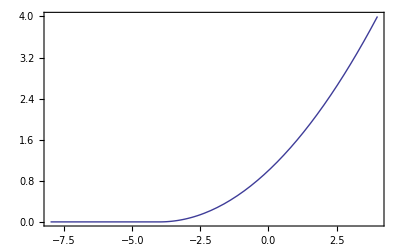

Derivative of penfuncsqr:

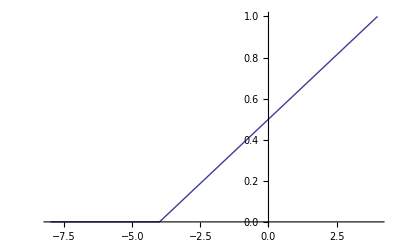

Exponential quadratic penalty function penfuncexpsqr:

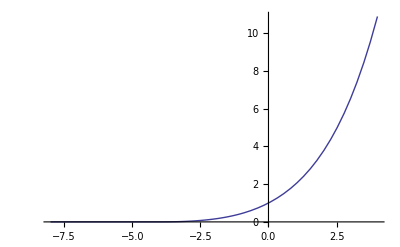

Derivative of penfuncexpsqr:

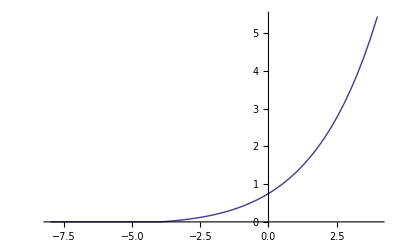

Penalty function with a jump - penfuncjump:

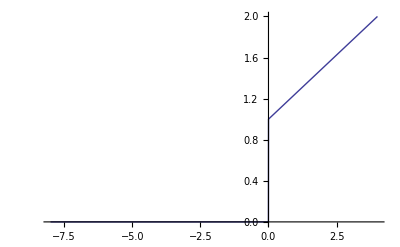

Derivative of penfuncjump:

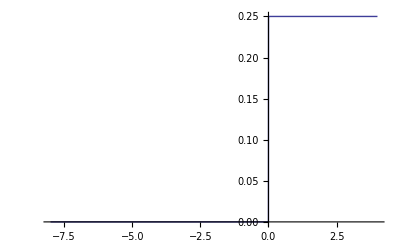

```mathematica
Module[{d=4,h=1,k,func=penfuncsqr,derfunc=derpenfuncsqr},
If[testmode≠0,
k:=h/d;
Print["d = ",d,", h = ",h,", k = ",k];
(* Square penalty function: *)
plpenfuncsqr=Plot[penfuncsqr [c,{d,h}],  {c,-2*d,d} , 
PlotRange->All,Frame->True];
plderpenfuncsqr=Plot[derpenfuncsqr [c,{d,h}],  {c,-2*d,d} , PlotRange->All];

(* Exponential-quadratic penalty function: *)
plpenfuncexpsqr=Plot[penfuncexpsqr [c,{d,h}],  {c,-2*d,d} , PlotRange->All];
plderpenfuncexpsqr=Plot[derpenfuncexpsqr [c,{d,h}],  {c,-2*d,d} , PlotRange->All];

(* Jump penalty function: *)
plpenfuncjump=Plot[penfuncjump [c,{h,k}],  {c,-2*d,d} , PlotRange->All];
plderpenfuncjump=Plot[derpenfuncjump [c,{h,k}],  {c,-2*d,d} , PlotRange->All];

];
];

(* Show the graphs: *)
If[testmode≠0,
Print["Penalty function penfuncsqr:"];
Show[   plpenfuncsqr   ]   ]
If[testmode≠0,
Print["Derivative of penfuncsqr:"];
Show[   plderpenfuncsqr   ]  ]

If[testmode≠0,
Print["Exponential quadratic penalty function penfuncexpsqr:"];
Show[   plpenfuncexpsqr   ]   ]
If[testmode≠0,
Print["Derivative of penfuncexpsqr:"];
Show[   plderpenfuncexpsqr   ]  ]

If[testmode≠0,
Print["Penalty function with a jump - penfuncjump:"];
Show[   plpenfuncjump   ]   ]
If[testmode≠0,
Print["Derivative of penfuncjump:"];
Show[   plderpenfuncjump   ]  ]
```

### Tests (penalty functions):

#### Test of penalty generating functions :

```mathematica
If[  testmode≠   0   ,
ccc=-0.001023;

penfunc=penfuncexp;
derpenfuncarg=derpenfuncexp;

penfunc=penfuncexpsqr;
derpenfuncarg=derpenfuncexpsqr;

Needs["NumericalCalculus`"];
Print[   derpenfuncarg[ccc,param]    ];
Print[   D[penfunc[x,param],x]  /. x->ccc    ];
Print[   ND[penfunc[x,param],x,ccc]    ];
]
```

2.99292

2.99292

2.99292

#### Tests with anfuncsimpconstr :

```mathematica
If   [   testmode≠0, 
(* Input data: *)
param={0,0,0};
param={1.1,1.1,1.1};
param={1.01,1.01,1.01};
param={1.01,1.01};
calcobj=calcconstr=calcgradobj=calcgradconstr=1;
anfuncorig=anfuncsimpconstr;
ancdorig={"an cd orig"};

(* Penalty generating function: *)

penfunc=penfuncexp;
derpenfuncarg=derpenfuncexp;

penfunc=penfuncexpsqr;
derpenfuncarg=derpenfuncexpsqr;

penparam={dd,hh}={0.1,1.00001};
defderpenfunc= 22563 ;  (* flag for whether penalty function is defined or not *)

keepconstraints=123;  (* flag for whether to keep constraints in the oeriginal function *)


(* parameters (penalty deifnition data) arranged for output: *)
argtab:=Transpose[{{"anfuncorig","ancdorig","penfunc","penparam","defderpenfunc","derpenfuncarg","keepconstraints"},{anfuncorig, ancdorig,  penfunc, penparam,  defderpenfunc, derpenfuncarg, keepconstraints }}];

(* Form definition data for penalty analysis function: *)
cdpen := {  anfuncorig, ancdorig,  penfunc, penparam,  defderpenfunc, derpenfuncarg, keepconstraints  };


anres=anfuncorig[param,1,1,1,1,ancdorig];
penres=penaltyanfunc[param,1,1,1,1,cdpen ];

(*   Extract objective & constraint functions values, calculate penalty terms   *)
tabconstr=anres[[4]];
tabgradconstr=anres[[8]];
objfunc=anres[[2]];
gradobjfunc=anres[[6]];
penobjfunc=penres[[2]];
pengradobjfunc=penres[[6]];

penterms=Table[
{
tabconstr[[i]],
penfunc[tabconstr[[i]],penparam],
tabgradconstr[[i]]  *  derpenfuncarg[tabconstr[[i]],penparam]
},  {i,1,Length[tabconstr]}
];
tabpenterms=Join[{{"constraint f.","penalty term","penalty term derivative"}},penterms];

(*    Calculate penalty addition (sum of penalty terms) and its gradient:    *)
penalty=Sum[penterms[[i,2]],{i,1,Length[penterms]}];
gradpenalty=Sum[penterms[[i,3]],{i,1,Length[penterms]}];

Print["\n\n\nDefinition data for penalty analysis function: \n", TableForm[argtab]   ];
Print["\nOriginal analysis results: \n  ",anres];
Print["\nPenalty analysis function results: \n  ",penres];

Print["\nPenalty terms: \n",TableForm[tabpenterms]];

Print["\nObjective function (original): ",objfunc];
Print["Penalty function (calculated by hand): ",objfunc+penalty];
Print["Penalty function (from pen. analysis): ",penobjfunc];

Print["\nGradient of objective function (original): ",gradobjfunc];
Print["Gradient of penalty function (calculated by hand): ",gradobjfunc+gradpenalty];
Print["Gradient of penalty function (from pen. analysis): ",pengradobjfunc];
]
```

Definition data for penalty analysis function: 
anfuncorig | anfuncsimpconstr
ancdorig | an cd orig
penfunc | penfuncexpsqr
penparam | 0.1
1.00001
defderpenfunc | 22563
derpenfuncarg | derpenfuncexpsqr
keepconstraints | 123

Original analysis results: 
  {1.,2.0402,1.,{-0.015,-0.02},1.,{2.02,2.02},1.,{{-1.5,0.},{0.,-2.}},0.}

Penalty analysis function results: 
  {1.,3.18606,1.,{-0.015,-0.02},1.,{-29.2563,-34.6595},1.,{{-1.5,0.},{0.,-2.}},0.}

Penalty terms: 
constraint f. | penalty term | penalty term derivative
-0.015 | 0.621868 | -31.2763
0.
-0.02 | 0.523993 | 0.
-36.6795

Objective function (original): 2.0402

Penalty function (calculated by hand): 3.18606

Penalty function (from pen. analysis): 3.18606

Gradient of objective function (original): {2.02,2.02}

Gradient of penalty function (calculated by hand): {-29.2563,-34.6595}

Gradient of penalty function (from pen. analysis): {-29.2563,-34.6595}

```mathematica
(* Test for changing composition of the definition data for the penalty function - change this   *)
If[testmode≠0,
cdpen := {  anfuncorig, ancdorig,  penfunc, penparam,  defderpenfunc, derpenfuncarg, keepconstraints  };

cdpen := {  anfuncorig, ancdorig,  penfunc, penparam  };

keepconstraints=0;
penfunc=penfuncexpsqr;
derpenfuncarg=derpenfuncexpsqr;

defderpenfunc=   1   ;

If[defderpenfunc==0,
derpenfuncarg=nofunc;
];

penaltyanfuncconstr[param,1,1,1,1,cdpen ]
]
```

{1.,3.18606,1.,{-0.015,-0.02},1.,{-29.2563,-34.6595},1.,{{-1.5,0.},{0.,-2.}},0.}

## Numerical gradients, gradient checks & analysis transforms

### Selsection of parameters

parindtonames [select, paramnamesall]
   - Creates a list of parameter names selected from paramnamesall (a list of all parameter names) that corresponds to parameter indices in selection list selsct. select can be arbitrarily nested list. 
getgradsel [grad, select]
    - Returns a reduced gradient according to reduced parameters select, where full gradient (with respect to all parameters) is grad.
setparamsel [p0, select, paramall] - returns a full parameter list if p0 is a reduced set of parameters, select is a list of indices of parameters in the full set corresponding to parameters from reduced set, and paramall is a list of default values for the full set of parameters.

Form of selection indices:
{p1, {p21, p22, p23}, p3, p4} means the following: 1st parameter from reduced set defines parameter with index p1 in the full set, 2nd parameter from the reduced set defines parameters p21, p22, p23 from the full set, 3rd parameter form the reduced set defines parameter p3 from the full set, and 4th parameter from the reduced set defines the parameter with index p4 in the full set. Other parameters in the full set have referential values defined in paramall.

```mathematica
parindtonames[select_,paramnamesall_]:=Module[{ret,cur,i},
(* Converts a parameter selection list containing indices to a list containing names: *)
If[Depth[select]==1,Return[paramnamesall[[select]]]];
(*
Table[paramnamesall[[select[[i]]]],{i,1,Length[select]}]
*)
Table[parindtonames[select[[i]],paramnamesall],{i,1,Length[select]}]
];

getgradsel[ grad_,select_]:=Module[{gradsel,val,depend,i,j},
(* Change gradient with respect to all parameters to gradient with respect to selected parameters: *)
gradsel={};
(*   Print["grad: " ,grad]   *)
For[i=1,i≤Length[select],i=i+1,
depend=select[[i]];
If[Depth[depend]<2,
depend={depend};    (* generic parameters that depend on a specific parameter *)
];
AppendTo[gradsel,
Sum[grad[[ depend[[j]] ]],{j,1,Length[depend]}]
];
(*  Print["i: ",i,", depend: ",depend,", gradsel: ",gradsel]  *)
];
gradsel
];


setparamsel[p0_,select_,paramall_]:=Module[{ret,cur,i,j,p,depend},
(* Sets generic parameters according to reduced parameters and selection list: *)
p=paramall;
For[i=1,i≤Length[select],i=i+1,
depend=select[[i]];
If[Depth[depend]<2,
depend={depend};    (* indices of generic parameters that depend on a specific parameter *)
];
For[j=1,j≤Length[depend],j=j+1,
p[[depend[[j]] ]]=p0[[i]];
];
];
p
];
```

### Numerical gradient analysis function anfuncnumgrad [..., {anfunc, ancd, step, <results>} ] ... are standard parameters of analysis functions, and definition data consists of the analysis function (anfunc, symbol), definition data passed to this function (ancd), and step size for numerical definition (step, can be vector or scalar - in this case teh same step is used for all parameters). ... = param, calcobj, calcconstr, calcgradobj, calcgradconstr Definition data can also contain results, in which case actual analysis does not need to be performed, but these results are used for unperturbed parameters. This can be used if results at unperturbed parameters have been calculated elsewhere.

```mathematica
anfuncnumgrad[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{retcalcobj=calcobj,retcalcconstr=calcconstr,retcalcgradobj=calcgradobj,retcalcgradconstr=calcgradconstr,ret=0,
calcobj1,calcconstr1,calcgradobj1,calcgradconstr1,ret1,
p2,
calcobj2,calcconstr2,calcgradobj2,calcgradconstr2,ret2,
obj1=0,constr1={},gradobj1={},gradconstr1={},obj2=0,constr2={},gradobj2={},gradconstr2={},
result, 
anfunc, ancd ,
i,j},
(* $A Igor feb06; *)

anfunc=cd[[1]];
ancd=cd[[2]];
step=cd[[3]];
If[Depth[step]<2,
step=Table[step,{i,1,Length[p]}];
];

If[Length[cd]>3,
(* Results at unperturbed parameters are already available, we just copy these results: *)
result={calcobj1,obj1,calcconstr1,constr1,calcgradobj1,gradobj1,calcgradconstr1,gradconstr1,ret1}=cd[[4]],
(* Results at unperturbed parameters are not available, perform calculation: *)
result={calcobj1,obj1,calcconstr1,constr1,calcgradobj1,gradobj1,calcgradconstr1,gradconstr1,ret1}= anfunc[p,1,1,1,1,ancd];
];

gradobj1=Table[0,{i,1,Length[p]}];
If[Length[constr1]>0,
gradconstr1=Table[Table[0,{j,1,Length[p]}],{i,1,Length[constr1]}];
];

(* Note in returned value if something could not be calcuated: *)
If[calcobj1==0,
retcalcobj=retcalcgradobj=0;
If[calcobj≠0 || calcgradobj≠0,ret=-1];
];
If[calcconstr1==0,
retcalcconstr=retcalcgradconstr=0;
If[calcconstr≠0 || calcgradconstr≠0,ret=-1];
];

If[debugmode≠0,
Print["Perturbed component ",0,", parameters: ",N[p],", Analysis result: \n  ",N[result],"\nObjective gradient: ",N[gradobj1]," Constraint gradients: ",N[gradconstr1]];
];

For[i=1,i≤Length[p],i=i+1,
(* analysis with parameter i perturbed: *)
p2=p;
p2[[i]]=p2[[i]]+step[[i]];
result={calcobj2,obj2,calcconstr2,constr2,calcgradobj2,gradobj2,calcgradconstr2,gradconstr2,ret2}= anfunc[p2,1,1,0,0,ancd];
(* Note in returned value if something could not be calcuated: *)
If[calcobj2==0,
retcalcobj=retcalcgradobj=0;
If[calcobj≠0 || calcgradobj≠0,ret=-1];
,
(* By the difference, calculate component of objective gradient: *)
gradobj1[[i]]=(obj2-obj1)/step[[i]];
];
If[calcconstr2==0,
retcalcconstr=retcalcgradconstr=0;
If[calcconstr≠0 || calcgradconstr≠0,ret=-1];
,
(* By the difference, calculate components of constraint gradients: *)
For [j=1,j≤Length[constr1],j=j+1,
gradconstr1[[j,i]]=(constr2[[j]]-constr1[[j]])/step[[i]];
];
];

If[debugmode≠0,
Print["Perturbed component ",i,", parameters: ",N[p2],", Analysis result: \n  ",N[result],"\nObjective gradient: ",N[gradobj1]," Constraint gradients: ",N[gradconstr1]];
];

];
Return[
{retcalcobj,obj1,
retcalcconstr,constr1,
retcalcgradobj,gradobj1,
retcalcgradconstr,gradconstr1,
ret}
];
];
```

### Test of analytical gradients returned by an analysis function: testangrad [anfunc, ancd, param, step] - compares analytical gradient of objective and constraint functions calculated by anfunc with numerical gradients. anfunc - analysis functios that is checked ancd - definition data for anfunc param - parameters at which check is performed step - step size for numerical differentiation; It can be a number (the same step used for all components) or a vector (different step sizes for different components)

```mathematica
testangrad[anfunc_,ancd_,param_,step_]:=Module[{
calcobj1,calcconstr1,calcgradobj1,calcgradconstr1,ret1,
calcobj2,calcconstr2,calcgradobj2,calcgradconstr2,ret2 },
(* $A Igor feb06; *)

{calcobj1,obj1,calcconstr1,constr1,calcgradobj1,gradobj1,calcgradconstr1,gradconstr1,ret1}= anfunc[param,1,1,1,1,ancd];

{calcobj2,obj2,calcconstr2,constr2,calcgradobj2,gradobj2,calcgradconstr2,gradconstr2,ret2}=anfuncnumgrad[param,1,1,1,1,{anfunc,ancd,step}];

If[calcobj1≠0,
Print["Objective function gradient:"];
Print["Analytical:\n  ",N[gradobj1]];
Print["Numerical:\n  ",N[gradobj2]];
Print["Difference:\n  ",N[gradobj1-gradobj2]];
Print["Relative difference:\n  ",N[(gradobj1-gradobj2)/gradobj1]];
];

If[calcconstr1≠0,
Print["\n\nConstraint functions gradients:"];
Print["Analytical:\n  ",N[gradconstr1]];
Print["Numerical:\n  ",N[gradconstr2]];
Print["Difference:\n  ",N[gradconstr1-gradconstr2]];
Print["Relative difference:\n  ",N[(gradconstr1-gradconstr2)/gradconstr1]];
];
];
```

#### Test of gradients for testanfunc1:

```mathematica
If[testmode≠0,
testangrad[anfuncsimpconstr,"3",{3,3,3},10^-5];
,,]
```

```mathematica
If[testmode≠0,
param={1,1};
testangrad[testanfunc1,"cd",param,10^-6]  ;
,,]
```

```mathematica
If[testmode≠0,
param
,,]
```

```mathematica
If[testmode≠0,
testanfunc1[param,1,1,1,1,"cd"]
,,]
```

```mathematica
If[testmode≠0,
anfuncnumgrad[param,1,1,1,1,{testanfunc1,"cd",10^-6}]
,,]
```

```mathematica
If[testmode≠0,
testanfunc1[param,1,1,1,1,"cd"]
,,]
```

## Manipulating tables of analysis resuts

Analysis and algorithm history
Note: for history records, choose another file than for other purposes, since this file is often deleted
algorithm history is usually reset by each algorithm, as opposed to analysis history, where analysis points are continuously appended to the current history.

### Initialization of global history variables:

```mathematica
recanhistory=1;   (* whether to record analysis history *)
recalghistory=1;   (* whether to record algorithm history *)
noteanhistory=0;   (* whether to print notifications when recording an. history *)
notealghistory=0;   (* whether to print notifications when recording alg. history *)
rewriteanhistory=1;  (* when writing to file, rewrite previous history *)
rewritealghistory=1;  (* when writing to file, rewrite previous history *)
anhistory={};      (* analysis histry (table of analysis points) *)
alghistory={};      (* algorithm histry (table of analysis points or their tables) *)
saveanhistory={};
savealghistory={};
fileanhistory="anhistory.out";  (* file where analysis history is recorded *)
filealghistory="alghistory.out";    (* file where algorithm history is recorded *)
```

### Functions for manipulating analysis and algorithm history:

```mathematica
(resetalghistory[]:=resetalghistory[recalghistory,filealghistory];) (resetalghistory[record_,filename_]:=Module[{},recalghistory=record;filealghistory=filename;alghistory={};savealghistory={};];) (resetanhistory[]:=resetanhistory[recanhistory,fileanhistory];) (resetanhistory[record_,filename_]:=Module[{},recanhistory=record;fileanhistory=filename;anhistory={};saveanhistory={};];) (resethistory[record_,filename_]:=Module[{},resetalghistory[record,filename];resetanhistory[record,filename];];) (resethistory[]:=Module[{},resetalghistory[];resetanhistory[];];) (storealghistory[functionname_,table_]:=Module[{},If[recalghistory||recalghistory≠0,If[notealghistory||notealghistory≠0,Print[functionname,": Algorithm progress stored to variable \"alghistory\"."];];alghistory=table;If[Head[filealghistory]==String,If[StringLength[filealghistory]>0,If[rewritealghistory||rewritealghistory≠0,Put["Algorithm hisrory file",DateList[],filealghistory];];PutAppend["Algorithm history, from "<>ToString[functionname]<>"; date:",DateList[],filealghistory];Save[filealghistory,alghistory];];];];];) (appendalghistory[functionname_,elemet_]:=Module[{},If[recalghistory||recalghistory≠0,If[notealghistory||notealghistory≠0,Print[functionname,": Algorithm history appended, variable \"alghistory\"."];];If[Depth[alghistory]<2,alghistory={};];AppendTo[alghistory,elemet];If[Head[filealghistory]==String,If[StringLength[filealghistory]>0,If[rewritealghistory||rewritealghistory≠0,Put["Algorithm hisrory file",DateList[],filealghistory];];PutAppend["Algorithm history, from "<>ToString[functionname]<>"; date:",DateList[],filealghistory];Save[filealghistory,alghistory];];];];];) (storeanhistory[functionname_,table_]:=Module[{},If[recanhistory||recanhistory≠0,If[noteanhistory||noteanhistory≠0,Print[functionname,": Table of analysis points stored to variable \"anhistory\"."];];anhistory=table;If[Head[fileanhistory]==String,If[StringLength[fileanhistory]>0,If[rewriteanhistory||rewriteanhistory≠0,Put["Analysis hisrory file",DateList[],fileanhistory];];PutAppend["Analysis history, from "<>ToString[functionname]<>"; date:",DateList[],fileanhistory];Save[fileanhistory,anhistory];];];];];) (appendanhistory[functionname_,elemet_]:=Module[{},If[recanhistory||recanhistory≠0,If[noteanhistory||noteanhistory≠0,Print[functionname,": Analysis history appended, variable \"anhistory\"."];];If[Depth[anhistory]<2,anhistory={};];AppendTo[anhistory,elemet];If[Head[fileanhistory]==String,If[StringLength[fileanhistory]>0,If[rewriteanhistory||rewriteanhistory≠0,Put["Analysis hisrory file",DateList[],fileanhistory];];PutAppend["Analysis history, from "<>ToString[functionname]<>"; date:",DateList[],fileanhistory];Save[fileanhistory,anhistory];];];];];)
```

Null^10

### Tests of functions for manipulating analysis and algorithm history:

```mathematica
If[testmode≠0,
(*
fileanhistory  =  filealghistory=  "test.out";
recanhistory=1;
recalghistory=1;
noteanhistory=1;
notealghistory=1;
*)
(* Empty contents of history files: *)
Put["Beginning of history file.",filealghistory];
,,]
```

#### Storing complete algorihm history:

```mathematica
If[testmode≠0,
storealghistory["testfunction",{"algel1","algel2"}];
Import[filealghistory,"Text"]
,,]
```

#### Appending data to algorihm history:

```mathematica
If[testmode≠0,
appendalghistory["testfunction","New element"];
Import[filealghistory,"Text"]
,,]
```

#### Storing complete analysis history:

```mathematica
If[testmode≠0,
storeanhistory["testanalysisfunction",{"analysis1","analysis2"}];
Import[fileanhistory,"Text"]
,,]
```

#### Appending data to analysis history:

```mathematica
If[testmode≠0,
appendanhistory["testanalysisfunction","New analysis"];
Import[filealghistory,"Text"]
,,]
```

Calculating factors and intervals for tables with geometrical growth of interval lengths:

#### Factors for tables with specified edge points:

```mathematica
tabexpfactors[numpt_,fact_]:=tabexpfactint[numpt,fact][[1]];

tabexpfactint[numptarg_,fact_]:=Module[{ret,numpt,sumint,intervals,factors},
(* $A Igor mar06; *)
numpt=Round[numptarg];
intervals=Table[0,{i,1,numpt-1}];
factors=Table[0,{i,1,numpt}];
inter=1;    (* current interval (non-normalized) *)
sumint=0;  (* sum of intervals - normalizing factor at the end *)
For[i=1,i<numpt,i=i+1,
intervals[[i]]=inter;
sumint=sumint+inter;
factors[[i+1]]=sumint;
inter=inter*fact;
];
intervals=intervals/sumint;
factors=factors/sumint;
N[ {factors,intervals} ]
];
```

#### Factors for tables with specified central and edge point:

```mathematica
tabexpfactorscent[numpt_,fact_]:=Module[{},
(* $A Igor mar06; *)
If[Mod[numpt,2]==0,
Return[tabexpfactorscent[numpt+1,fact]];
];
Join[
Reverse[
Drop[
-tabexpfactors[(numpt+1)/2,fact],
1]
],
tabexpfactors[(numpt+1)/2,fact]
]
];

tabexpfactintcent[numpt_,fact_]:=Module[{factors,i},
(* $A Igor mar06; *)
factors=tabexpfactorscent[numpt,fact];
Return[{factors,
Table[factors[[i+1]]-factors[[i]],{i,1,Length[factors]-1}]
}];
];
```

Function for calculating  analysis points and tables of analysis points:

```mathematica
testpoint=calcanpt[anfuncsimpconstr,{1.11,2.22},11,22,33,44,"1"]
```

calcanpt[anfuncsimpconstr,{1.11,2.22},11,22,33,44,1]

Analysis point is a list that consists at least of 3 parts:
    { param, res, args, ... }
where param is a vector of parameters, res is a vector of results, args are arguments {calcobj, calcconstr, calcgradobj and calcgradconstr, cd} passed to the analysis function. Further arguments are lists of indices and lists of factors, and there can be even further arguments, too.
  param = { p1, p2, ... }
  res = { calcobj, obj, calcconstr, { c1, c2, ... }, calcgradobj, { DoDp1, DobjDp2, ... }, calcgradconstr, { { Dc1Dp1, Dc1Dp2, Dc1Dp3, ... }, {  Dc2Dp1, Dc2Dp2, Dc2Dp3, ... }, ret  }
  args = { reqcalcobj, reqcalcconstr, reqcalcgradobj, reqcalcgradconstr, cd }
  calcobj, calcconstr, calcgradobj, calcgradconstr - calculation flags that tell whether the objective function, constraints, gradients of the objective function and gradients of constraints have been calculated (0 for no and non-zero for yes)
  reqcalcobj, reqcalcconstr, reqcalcgradobj, reqcalcgradconstr - request flags that request calculation of given quantities, as were passed to the analysis
  cd - definition data passed to the analysis function
  p1, p2, ... - values of optimization parameters at which analysis has been performed
  obj - value of the objective function
  c1, c2, c3 - values of the constraint functions
  DoDp1, DoDp2, DoDp3 - derivatives of the objective function with respect to individual parameters (components of objective function gradient)
  Dc1Dp1, Dc1Dp2, ..., Dc2Dp1, ... - derivatives of individual constraint functions with respect to optimization parameters (components of constraint gradients)
  ret - error code of analysis (0 for no error)
  
Example:
{ {1.11, 2.22}, { 1, 6.1605, 1, {-0.165, -2.44} , 1, {2.22, 4.44}, 1, { {-1.5, 0.}, {0., -2.} }, 0 }, { 1, 1, 1, 1, "3" }}

#### calcanpt [anfunc, p, calcobj, calcconstr, calcgradobj, calcgradconstr, cd] runs analysis defined by anfunc at parameters p and with specification arguments calcobj, calcconstr, calcgradobj, calcgradconstr, cd for the analysis

```mathematica
calcanpt[analysisfunction_,p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=
(* $A Igor mar06; *)
{
p,
analysisfunction[p,calcobj,calcconstr,calcgradobj,calcgradconstr,cd],
{calcobj,calcconstr,calcgradobj,calcgradconstr,cd}
}
```

#### Functions that extract information from analysis points: anptparam, anptres, anptarg, anptind, anptfact, anptcalcobj, anptobj, ..., anptret, anptargcalcobj, ..., anptargspec

```mathematica
(* $A Igor mar06; *)

(* Parameters: *)
anptparam[pt_]:=If[Length[pt]≥1,
Return[pt[[1]]],
Print["Error in anptparam: Invalid structure of analysis point.\n"];
Return[{}];
];

(* Specific parameter: *)
anptparami[pt_,i_]:=Module[{param},
param=anptparam[pt];
If[Length[param]≥Abs[i],
Return[param[[i]]],
Print["Error in anptparami: index ",i," out of range ",Length[param]];
Return[0];
];
];

(* Results: *)
anptres[pt_]:=If[Length[pt]≥2,
Return[pt[[2]]],
Print["Error in anptres: Invalid structure of analysis point, less than 2 elements.\n"];
Return[{}];
];

(* Results - calculated flag for objective function: *)
anptcalcobj[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥1,
Return[res[[1]]],
Print["Error in anptcalcobj: Invalid structure of analysis resuts: ",res];
Return[0];
];
];

(* Results - objective function: *)
anptobj[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥2,
Return[res[[2]]],
Print["Error in anptobj: Invalid structure of analysis resuts: ",res];
Return[0];
];
];


(* Results - calculation flag for gradient of objective function: *)
anptcalcgradobj[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥5,
Return[res[[5]]],
Print["Error in anptcalcgradobj: Invalid structure of analysis resuts: ",res];
Return[0];
];
];

(* Results - gradient of objective function: *)
anptgradobj[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥6,
Return[res[[6]]],
Print["Error in anptgradobj: Invalid structure of analysis resuts: ",res];
Return[0];
];
];


(* Results - calculation flag for constraint functions: *)
anptcalcconstr[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥3,
Return[res[[3]]],
Print["Error in anptcalcconstr: Invalid structure of analysis resuts: ",res];
Return[0];
];
];

(* Results - constraint functions: *)
anptconstr[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥4,
Return[res[[4]]],
Print["Error in anptconstr: Invalid structure of analysis resuts: ",res];
Return[0];
];
];


(* Results - calculation flag for gradients of constraint functions: *)
anptcalcgradconstr[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥7,
Return[res[[7]]],
Print["Error in anptcalcgradconstr: Invalid structure of analysis resuts: ",res];
Return[0];
];
];

(* Results - gradients of constraint functions: *)
anptgradconstr[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥8,
Return[res[[8]]],
Print["Error in anptgradconstr: Invalid structure of analysis resuts: ",res];
Return[0];
];
];

(* Results - return value: *)
anptret[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥9,
Return[res[[9]]],
Print["Error in anptret: Invalid structure of analysis resuts: ",res];
Return[0];
];
];

(* Arguments to analysis function: *)
anptarg[pt_]:=If[Length[pt]≥3,
Return[pt[[3]]],
Print["Error in anptarg: Invalid structure of analysis point, less than 3 elements.\n"];
Return[{}];
];

(* Arguments to analysis function - calculation request for objective function: *)
anptargcalcobj[pt_]:=Module[{args},
args=anptargs[pt];
If[Length[args]≥1,
Return[args[[1]]],
Print["Error in anptargcalcobj: Invalid structure of analysis specification arguments (should be {calcobj, calcconstr, calcgradobj, calcgradconstr, cd}): ",args];
Return[0];
];
];

(* Arguments to analysis function - calculation request for constraint functions: *)
anptargcalcconstr[pt_]:=Module[{args},
args=anptargs[pt];
If[Length[args]≥2,
Return[args[[2]]],
Print["Error in anptargcalcconstr: Invalid structure of analysis specification arguments (should be {calcobj, calcconstr, calcgradobj, calcgradconstr, cd}): ",args];
Return[0];
];
];

(* Arguments to analysis function - calculation request for gradient of objective functions: *)
anptargcalcgradobj[pt_]:=Module[{args},
args=anptargs[pt];
If[Length[args]≥3,
Return[args[[3]]],
Print["Error in anptargcalcgradobj: Invalid structure of analysis specification arguments (should be {calcobj, calcconstr, calcgradobj, calcgradconstr, cd}): ",args];
Return[0];
];
];

(* Arguments to analysis function - calculation request for gradient of objective functions: *)
anptargcalcgradconstr[pt_]:=Module[{args},
args=anptargs[pt];
If[Length[args]≥4,
Return[args[[4]]],
Print["Error in anptargcalcgradconstr: Invalid structure of analysis specification arguments (should be {calcobj, calcconstr, calcgradobj, calcgradconstr, cd}): ",args];
Return[0];
];
];

(* Arguments to analysis function - specification argument: *)
anptargspec[pt_]:=Module[{args},
args=anptargs[pt];
If[Length[args]≥5,
Return[args[[5]]],
Print["Error in anptargspec: Invalid structure of analysis specification arguments (should be {calcobj, calcconstr, calcgradobj, calcgradconstr, cd}): ",args];
Return[0];
];
];

(* Table indices: *)
anptind[pt_]:=If[Length[pt]≥4,
Return[pt[[4]]],
Print["Error in anptind: Table indices are not available for this analysis point.\n"];
Return[{}];
];

(* Table factors: *)
anptfact[pt_]:=If[Length[pt]≥5,
Return[pt[[5]]],
Print["Error in anptfact: Table factors are not available for this analysis point.\n"];
Return[{}];
];
```

#### tabanptrand [num,anfunc, p1, p2, calcobj, calcconstr, calcgradobj, calcgradconstr, cd] num - number of analyses performed anfunc - analysis function p1 - lower limitd for parameters p2 - upper limits for parameters calcoj, calcconstr, calcgradobj, calcgradconstr - calculation flags for analysis cd - definition data for analysis Runs a set of analyses defined by anfunc in random points on the iterval specified by interval limits p1 and p2, with specification arguments calcobj, calcconstr, calcgradobj, calcgradconstr, cd for individual analyses. Function can have an additional argument, which instructs (if different than 0) to print intermediate results after calculation of each complete row of the table. Returns a list of analysis points with indices and factors appended to the standard analysis data. The form of results is { { {param_1}, {analysisresults_1}, {specargs_1}, {index_1}, {factor_1} }, { {param_2}, {analysisresults_2}, {specargs_2}, {index_2}, {factor_2} }, ..., } where param_i is vector of parameters at which the i-th analysis of the table is performed, analysisresults_i is a list of results of this analysis (in the standard form), specargs_i is the list of specification arguments at which the analysis was called, index_i is the index of a particular analysis (running from 1 to Length[factors]), and factor_i contains the list of random numbers used for calculation of parameters. tabanptrand - similar fut central value for parameters and interval lengths are specified as p1 and p0.

```mathematica
tabanptrand[num_,anfunc_,p1_,p2_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=tabanptrand[num,anfunc,p1,p2,calcobj,calcconstr,calcgradobj,calcgradconstr,cd,0];
tabanptrand[num_,anfunc_,p1_,p2_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_,printpartialresults_]:=Module[{i,j,k,tabk,ret,title,randfactors,randpar,t1,t2,t3,t4},Print["tabanptrand: lower lim.: ",p1,", upper lim.: ",p2];ret={};For[i=1,i≤num,i=i+1,t1=TimeUsed[];randfactors=Table[RandomReal[],{j,1,Length[p1]}];randpar=Table[p1⟦j⟧+randfactors⟦j⟧ (p2⟦j⟧-p1⟦j⟧),{j,1,Length[p1]}];t2=TimeUsed[];AppendTo[ret,Join[calcanpt[anfunc,randpar,calcobj,calcconstr,calcgradobj,calcgradconstr,cd],{{i}},{randfactors}]];t3=TimeUsed[];title="tabanptrand: partial results (up to el. "<>ToString[i]<>" of "<>ToString[num]<>"): ";If[printpartialresults≠0,Print[title,"\n",ret];];storealghistory[title,ret];];Return[ret];];
tabanptrandcent[num_,anfunc_,p0_,dp_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_,printpartialresults_]:=tabanptrand[num,anfunc,p0-0.5 dp,p0+0.5 dp,calcobj,calcconstr,calcgradobj,calcgradconstr,cd,printpartialresults];
tabanptrandcent[num_,anfunc_,p1_,p2_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=tabanptrandcent[num,anfunc,p1,p2,calcobj,calcconstr,calcgradobj,calcgradconstr,cd,0];
```

#### tabanpt1d [anfunc, p0, p1, factors, calcobj, calcconstr, calcgradobj, calcgradconstr, cd] Runs a table of analyses defined by anfunc on a line between p0 and p1, and with factors defining relative distances from p0 (expressed in ||p1-p0||), and specification arguments calcobj, calcconstr, calcgradobj, calcgradconstr, cd for individual analyses. Function can have an additional argument, which instructs (if different than 0) to print intermediate results after calculation of each complete row of the table. Returns an one dimensional list of analysis points with indices and factors appended to the standard analysis data. The form of results is { { {param_1}, {analysisresults_1}, {specargs_1}, {index_1}, {factor_1} }, { {param_2}, {analysisresults_2}, {specargs_2}, {index_2}, {factor_2} }, ..., } where param_i is vector of parameters at which th

```mathematica
tabanpt1d[anfunc_,p0_,p1_,factors_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=tabanpt1d[anfunc,p0,p1,factors,calcobj,calcconstr,calcgradobj,calcgradconstr,cd,0];

tabanpt1d[anfunc_,p0_,p1_,factors_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_,    printpartialresults_]:=
Module[{i,tabk,ret,title},
(* $A Igor mar06; *)
tabk=N[factors];
ret={};
For[i=1,i<=Length[tabk],i=i+1,
AppendTo[ret,
Join[
calcanpt[anfunc,p0+tabk[[i]]*(p1-p0),calcobj,calcconstr,calcgradobj,calcgradconstr,cd],
{{i}},{{tabk[[i]]}}
]
];

title=StringJoin["tabanpt1d: partial results (up to el. ",ToString[i]," of ",ToString[Length[tabk]],"): "];
If[printpartialresults≠0,
Print[title,"\n",ret];
];
(* Record progress of the table up to now, according to global control variables: *)
storealghistory[title,ret];

];

Return[ret];
];
```

#### tabanpt2d [anfunc, p0, p1, p2, factors1, factors2, calcobj, calcconstr, calcgradobj, calcgradconstr, cd] Runs a two dimensional table of analyses defined by anfunc on a plane defined by lines beteen (p0 and p1), and (p0 and p2), with factors defining relative distances from p0 (expressed in ||p1-p0|| and ||p1-p0||, respectively), and specification arguments calcobj, calcconstr, calcgradobj, calcgradconstr, cd for individual analyses. Otherwise the function works similar than tabanpt1d. Function can have an additional argument, which instructs (if different than 0) to print intermediate results after calculation of each complete row of the table. The returned analysis points are arranged in a 2 dimensional list, with the second index running faster. A two dimensional list of corresponding indices and a two dimensional list of corresponding factors are appended to each set of standard analysis point data. Function returns a two dimensional table of analysis points with lists of element indices and factors appended to standard analysis point data. The format of returned data is { {anpt_1_1, anpt_1_2, ...}, {anpt_2_1, anpt_2_2, ...}, ... } where the format of anpt_i_j is { {param_i_j}, {analysisresults_i_j}, {specargs_i}, {index_i_j}, {factor_i_j} } and {index_i_j} is a list of two indices and {factor_i_j} a list of two factors (along to the first and second direction, i.e. along (p1-p0) and (p2-p0)).

```mathematica
tabanpt2d[anfunc_,p0_,p1_,p2_,factors1_,factors2_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=tabanpt2d[anfunc,p0,p1,p2,factors1,factors2,calcobj,calcconstr,calcgradobj,calcgradconstr,cd,0];


tabanpt2d[anfunc_,p0_,p1_,p2_,factors1_,factors2_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_,    printpartialresults_]:=
Module[{i,j,tabk1,tabk2,ret},
(* $A Igor mar06; *)
tabk1=N[factors1];
tabk2=N[factors2];
ret={};
For[i=1,i≤Length[tabk1],i=i+1,
AppendTo[ret,
Table[
Join[
calcanpt[anfunc,p0+tabk1[[i]]*(p1-p0)+tabk2[[j]]*(p2-p0),calcobj,calcconstr,calcgradobj,calcgradconstr,cd],
{{i,j}},{{tabk1[[i]],tabk2[[j]]}}
],
{j,1,Length[tabk2]}
]
];

title=StringJoin["tabanpt2d: partial results (up to row ",ToString[i]," of ",ToString[Length[tabk1]],"): "];
If[printpartialresults≠0,
Print[title,"\n",ret];
];
(* Record progress of the table up to now, according to global control variables: *)
storealghistory[title,ret];

];  (* For *)
Return[ret];
];
```

#### flattentabanpt [ tab ] Returns a flattened table of analysis points tab in such a way that the returned table is a simple list of all analysis points contained in tab. If tab is a single analysis point (not a list of them) then {tab} is returned. If tab is a list of lists of analysis points then Flatten[tab] is returned, and so on recursively until the returned value is a simple 1D list of analysis points. Criteria for application of flattening is checking depth of res[[1,1]], which must be at the final stage vector of parameters of the first analysis point (with depth 1).

```mathematica
flattentabanpt[tab_]:=Module[{res},
(* $A Igor apr06; *)
If[Depth[tab[[1]] ]<2,
(* tab is not even a single analysis point, we return an empty table: *)
Print["\nError in flattentabanpt: Argument does not represent an analysis point or a table of analysis points:\n  ",tab,"\n"];
Return[{}];
];
If[Depth[tab[[1]] ] == 2,
(* tab is a single analysis point, we enclose it in a list to make a table: *)
Return[{tab}];
];
res=tab;
While[ Depth[res[[1,1]] ] >2,
res=Flatten[res,1];
];
Return[res];
];
```

#### convtabanpt1dpar [tab, whichpar] Converts a 1d table of analysis points tab in such a way that table factors (the 4th elements of analysis points in tables) are replaced by the value of a specific parameter whose index is specified by whichpar. The replaced table factors are put on the 6th position in tha analysis point structures contained in tab. This function is in useful for plotting of tables of analysis results when one wants to show a particular parameter on the x axis instead of a distance factor with respect to two edge points.

```mathematica
(* $A Igor apr06; *)


converttabanpt1dpar:=convtabanpt1dpar;
convvertbacktab1dpar:=convbacktab1dpar;

convtabanpt1dpar[tab_,whichpar_]:=Table[
{
tab[[i,1]],
tab[[i,2]],
tab[[i,3]],
tab[[i,4]],
{tab[[i,1,whichpar]]},
tab[[i,5]]
},
{i,1,Length[tab]}
];

convbacktab1dpar[tab_]:=Table[
{
tab[[i,1]],
tab[[i,2]],
tab[[i,3]],
tab[[i,4]],
tab[[i,6]]
},
{i,1,Length[tab]}
];
```

#### convtabanpt2dpar [tab, whichpar1, whichpar2] Converts a 2d table of analysis points tab in such a way that table factors (the 4th elements of analysis points in tables) are replaced by a pair of valus of two specific parameters whose indices are specified by whichpar1 and whichpar2. The replaced table factors are put on the 6th position in the analysis point structures contained in tab. This function is useful for plotting of tables of analysis results when one wants to show particular parameters on the x and y axes instead of a distance factor with respect to two edge points.

```mathematica
(* $A Igor apr06; *)

converttabanpt2dpar:=convtabanpt2dpar;
convvertbacktab2dpar:=convbacktab2dpar;

convtabanpt2dpar[tab_,whichpar1_,whichpar2_]:=
Table[
Table[
{
tab[[i,j,1]],
tab[[i,j,2]],
tab[[i,j,3]],
tab[[i,j,4]],
{ tab[[i,j,1,whichpar1]],tab[[i,j,1,whichpar2]] },
tab[[i,j,5]]
},   
{j,1,Length[tab[[i]] ]  }     ],
{i,1,Length[tab]}   ];

convbacktab2dpar[tab_]:=Table[
Table[
{
tab[[i,j,1]],
tab[[i,j,2]],
tab[[i,j,3]],
tab[[i,j,4]],
tab[[i,j,6]]
},   {j,1,Length[Tab[[i]]]  }  
],
{i,1,Length[tab]}
];
```

Functions for plotting tables of analysis results (including convergence history):

### Plotting 1D analysis tables:

#### plottabanpt1d [taban, plotpoints, plotlines, pointsize, linethickness, showplots] plots 1D tables of analysis points. taban - table of analysis points, ponts must be at the first level plotponts : if 0 or False then points are not plotted. plotlines : if 0 or False then lines are not plotted. pointsize : size of points on graphs linehickness: thickness of lines on graph showplots: if 0 or False then plots are not shown (but the returned table of plots can be shown later). Function called without this argument will show the plots. Function can also be called with last 2 or last 4 arguments omitted. In this case, default values are plotpoints=1, plotlines=1, pointsize=0.02, linethickness=0. Function returns a table of 4 plots: objective function plotted against table factors, constraint functions plotted agaainst table factors, objetive function plotted with respect to table indices, and constraint functions plotted with respect to table indices. These individual plots can be shown by Show[...,DisplayFunction->$DisplayFunction] when showing results is not requested at function call (i.e. th eartument showplots is 0 or False).

```mathematica
(plottabanpt1d[taban_,plotpoints_,plotlines_]:=plottabanpt1d[taban,plotpoints,plotlines,0.02,0];) (plottabanpt1d[taban_]:=plottabanpt1d[taban,1,1];) (plottabanpt1d[taban_,plotpoints_,plotlines_,pointsize_,linethickness_]:=plottabanpt1d[taban,plotpoints,plotlines,pointsize,linethickness,1];) (plottabanpt1d[taban_,plotpoints_,plotlines_,pointsize_,linethickness_,showplots_]:=Module[{i,j,dim,nconstr,npoints,parmin,parmax,tabparam,tabobj,tabconstr,tabind,tabfact,tabplotobjfact,tabplotconstrfact,tabplotobjind,tabplotconstrind,joined1,joined2},joined1=False;joined2=True;If[plotpoints==0||!plotpoints,joined1=True;];If[plotlines==0||!plotlines,joined2=False;];If[debugmode≠0,Print["plottabanpt1d: check 1"]];tabparam=Table[anptparam[taban⟦i⟧],{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 2"]];tabobj=Table[anptobj[taban⟦i⟧],{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 3"]];tabconstr=Table[anptconstr[taban⟦i⟧],{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 4"]];tabind=Table[anptind[taban⟦i⟧]⟦1⟧,{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 5"]];tabfact=Table[anptfact[taban⟦i⟧]⟦1⟧,{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 6"]];dim=Length[tabparam⟦1⟧];nconstr=Length[tabconstr⟦1⟧];npoints=Length[taban];If[debugmode≠0,Print["dim = ",dim,", nconstr = ",nconstr,", npoints = ",npoints]];If[debugmode≠0,Print["plottabanpt1d: check 7"]];tabplotobjind={{ListPlot[tabobj,PlotStyle->{Hue[1/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined1,PlotRange->All,DisplayFunction->Identity],ListPlot[tabobj,PlotStyle->{Hue[1/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined2,PlotRange->All,DisplayFunction->Identity]}};If[debugmode≠0,Print["plottabanpt1d: check 8"]];tabplotconstrind=Table[{ListPlot[Table[tabconstr⟦j,i⟧,{j,1,npoints}],PlotStyle->{Hue[(i+1)/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined1,PlotRange->All,DisplayFunction->Identity],ListPlot[Table[tabconstr⟦j,i⟧,{j,1,npoints}],PlotStyle->{Hue[(i+1)/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined2,PlotRange->All,DisplayFunction->Identity]},{i,1,nconstr}];If[debugmode≠0,Print["plottabanpt1d: check 9"]];tabplotobjfact={{ListPlot[Transpose[{tabfact,tabobj}],PlotStyle->{Hue[1/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined1,PlotRange->All,DisplayFunction->Identity],ListPlot[Transpose[{tabfact,tabobj}],PlotStyle->{Hue[1/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined2,PlotRange->All,DisplayFunction->Identity]}};If[debugmode≠0,Print["plottabanpt1d: check 10"]];tabplotconstrfact=Table[{ListPlot[Transpose[{tabfact,Table[tabconstr⟦j,i⟧,{j,1,npoints}]}],PlotStyle->{Hue[(i+1)/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined1,PlotRange->All,DisplayFunction->Identity],ListPlot[Transpose[{tabfact,Table[tabconstr⟦j,i⟧,{j,1,npoints}]}],PlotStyle->{Hue[(i+1)/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined2,PlotRange->All,DisplayFunction->Identity]},{i,1,nconstr}];If[debugmode≠0,Print["plottabanpt1d: check 11"]];If[showplots||showplots≠0,Print["\n\ntabplotobjfact (result[[1,1]]):\nValues of the objective function plotted against line factors:"] Show[tabplotobjfact,DisplayFunction->$DisplayFunction];If[debugmode≠0,Print["plottabanpt1d: check 12"]];Print["\n\ntabplotconstrfact (result[[1,2]])\nValues of constraint functions plotted against line factors; color order for constraints is like green->cyan->blue->red:"] Show[tabplotconstrfact,DisplayFunction->$DisplayFunction];If[debugmode≠0,Print["plottabanpt1d: check 13"]];Print["\n\ntabplotobjind (result[[2,1]])\nValues of the objective function plotted against analysis sequential numbers:"] Show[tabplotobjind,DisplayFunction->$DisplayFunction];If[debugmode≠0,Print["plottabanpt1d: check 14"]];Print["\n\ntabplotconstrind (result[[2,2]])\nValues of constraint functions plotted against analysis sequential numbers; color order for constraints is like green->cyan->blue->red:"] Show[tabplotconstrind,DisplayFunction->$DisplayFunction];If[debugmode≠0,Print["plottabanpt1d: check 15"]];];Print["Returned: {
{tabplotobjfact, tabplotconstrfact},
{tabplotobjind, tabplotconstrind},
{tabfact,tabobj,tabconstr}
}"];If[debugmode≠0,Print["plottabanpt1d: check 16"]];Return[{{tabplotobjfact,tabplotconstrfact},{tabplotobjind,tabplotconstrind},{tabfact,tabobj,tabconstr}}];If[debugmode≠0,Print["plottabanpt1d: check 17"]];];)
```

Null^4

### Plotting 2D analysis tables:

#### tabanpt2dgraph [ taban, linethickness, linecolor, pointsize, pointcolor, plotsolid, solidcolor, showplots ] grid of points in 2 or 3 dimensions. taban - 2D table of analysis points linethickness - line thickness, if greater than 0 then a grid of lines is plotted, otherwise it is not. linecolor - specification of line color (standard or accepted by handlecolor); if 0 then each row of points is connected by lines of different colors pointsize - size of points, if greater than 0 then points are plotted, otherwise they are not. pointcolor - specification of point color, similar effect as linecolor. plotsolid - if different than 0 then polygons (quadrilaterals) bound by points are plotted. solidcolor - color for solid polygons. showplots: if 0 or False then plots are not shown (but the returned table of plots can be shown later). Function called without this argument will show the plots. tabanpt2dgraph [ taban, size ] - plots points and lines, rows of points in different colors. tabanpt2dgraph [ taban, linethickness, linecolor ] - plots onlly line grid tabanpt2dgraph [ taban, linethickness, linecolor, pointsize, pointcolor ] - without solid polygons plottabanpt2d [taban, plotpoints, plotlines, pointsize, linethickness, showplots] plots 2d tables of analysis points. taban - 2D table of analysis points plotponts : if 0 or False then points are not plotted. plotlines : if 0 or False then lines are not plotted. pointsize : size of points on graphs linehickness: thickness of lines on graph showplots: if 0 or False then plots are not shown (but the returned table of plots can be shown later). Function called without this argument will show the plots. Function can also be called with last 2 or last 4 arguments omitted. In this case, default values are plotpoints=1, plotlines=1, pointsize=0.02, linethickness=0. Function returns a table of 4 plots: objective function plotted against table factors, constraint functions plotted agaainst table factors, objetive function plotted with respect to table indices, and constraint functions plotted with respect to table indices. These individual plots can be shown by Show[...,DisplayFunction->$DisplayFunction] when showing results is not requested at function call (i.e. th eartument showplots is 0 or False).

```mathematica
plottabanpt2d[taban_,plotpoints_,plotlines_]:=plottabanpt2d[taban,plotpoints,plotlines,0.02,0];
plottabanpt2d[taban_]:=plottabanpt1d[taban,1,1];
plottabanpt2d[taban_,plotpoints_,plotlines_,pointsize_,linethickness_]:=plottabanpt2d[taban,plotpoints,plotlines,pointsize,linethickness,1];
plottabanpt2d[taban_,plotpoints_,plotlines_,pointsize_,linethickness_,showplots_]:=plottabanpt2d[taban,plotpoints,plotlines,pointsize,linethickness,1,showplots];
plottabanpt2d[taban_,plotpoints_,plotlines_,pointsize_,linethickness_,plotsolids_,showplots_]:=tabanpt2dgraph[taban,If[plotlines==0,0,linethickness],0,If[plotpoints==0,0,pointsize],0,1,0,showplots];
tabanpt2dgraph[taban_,size_]:=tabanpt2dgraph[taban,size,0,size 20,0,0,0];
tabanpt2dgraph[taban_]:=tabanpt2dgraph[0.0008];
tabanpt2dgraph[taban_,linethickness_,linecolor_]:=tabanpt2dgraph[taban,linethickness,linecolor,0,0,0,0];
tabanpt2dgraph[taban_,linethickness_,linecolor_,pointsize_,pointcolor_]:=tabanpt2dgraph[taban,linethickness,linecolor,pointsize,pointcolor,0,0];
tabanpt2dgraph[taban_,linethickness_,linecolor_,pointsize_,pointcolor_,plotsolid_,solidcolor_]:=tabanpt2dgraph[taban,linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor,1];
tabanpt2dgraph[taban_,linethickness_,linecolor_,pointsize_,pointcolor_,plotsolid_,solidcolor_,showplots_]:=Module[{i,j,k,dim,nconstr,npoints,npoints1,npoints2,parmin,parmax,tabparam,tabobj,tabconstr,tabind,tabfact,tabplotobjfact,tabplotconstrfact,tabplotobjind,tabplotconstrind,joined1,joined2},joined1=False;joined2=True;If[plotpoints==0||!plotpoints,joined1=True;];If[plotlines==0||!plotlines,joined2=False;];tabparam=Table[Table[anptparam[taban⟦i,j⟧],{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}];tabobj=Table[Table[anptobj[taban⟦i,j⟧],{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}];tabconstr=Table[Table[anptconstr[taban⟦i,j⟧],{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}];tabind=Table[Table[anptind[taban⟦i,j⟧],{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}];tabfact=Table[Table[anptfact[taban⟦i,j⟧],{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}];dim=Length[tabparam⟦1,1⟧];nconstr=Length[tabconstr⟦1,1⟧];npoints1=Length[tabtest];npoints2=Length[tabtest⟦1⟧];npoints=npoints1 npoints2;tabplotobjfact=gridgraph[Table[Table[{tabfact⟦i,j,1⟧,tabfact⟦i,j,2⟧,tabobj⟦i,j⟧},{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}],linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor];tabplotobjind=gridgraph[Table[Table[{tabind⟦i,j,1⟧,tabind⟦i,j,2⟧,tabobj⟦i,j⟧},{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}],linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor];tabplotconstrfact=Table[gridgraph[Table[Table[{tabfact⟦i,j,1⟧,tabfact⟦i,j,2⟧,tabconstr⟦i,j,k⟧},{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}],linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor],{k,1,nconstr}];tabplotconstrind=Table[gridgraph[Table[Table[{tabind⟦i,j,1⟧,tabind⟦i,j,2⟧,tabconstr⟦i,j,k⟧},{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}],linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor],{k,1,nconstr}];If[showplots||showplots≠0,Print["\n\ntabplotobjfact ([[1,1]]):\nValues of the objective function plotted against line factors:"] Show[tabplotobjfact,DisplayFunction->$DisplayFunction,PlotRange->All,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"lf1","lf2","f   "}];Print["\n\ntabplotconstrfact ([[1,2]]\nValues of constraint functions plotted against line factors; color order for constraints is like green->cyan->blue->red:"] Show[tabplotconstrfact,DisplayFunction->$DisplayFunction,PlotRange->All,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"lf1","lf2","c_i   "}];Print["\n\ntabplotobjind ([[2,1]])\nValues of the objective function plotted against analysis sequential numbers:"] Show[tabplotobjind,DisplayFunction->$DisplayFunction,PlotRange->All,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"i1","i2","f   "}];Print["\n\ntabplotconstrind ([[2,2]])\nValues of constraint functions plotted against analysis sequential numbers; color order for constraints is like green->cyan->blue->red:"] Show[tabplotconstrind,DisplayFunction->$DisplayFunction,PlotRange->All,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"i1","i2","c_i   "}]];Print["Returned: {
{tabplotobjfact, tabplotconstrfact},
{tabplotobjind, tabplotconstrind}
}"];Return[{{tabplotobjfact,tabplotconstrfact},{tabplotobjind,tabplotconstrind}}];];
```

### Test of functions for manipulating tables of analyses:

#### Test: Function for calculating factors and intervals of a table with geometrically grown interval lengths:

```mathematica
If[testmode≠0,
numintervals=50;
intervalfactor=1.4;
tableofintervalsandfactors=tabexpfactint[numintervals,intervalfactor];

{"{last factor,first interval, last interval} = ",
{
tabexpfactint[numintervals,intervalfactor] [[1,-1]],
tabexpfactint[numintervals,intervalfactor] [[2,1]],
tabexpfactint[numintervals,intervalfactor] [[2,-1]]
}
}
,,]
```

```mathematica
If[testmode≠0,
numintervals=5;
intervalfactor=1.2;
tableofintervalsandfactors=tabexpfactint[numintervals,intervalfactor];

{"{factors, intervals, sum of intervals:} = ",
tableofintervalsandfactors[[1]],
tableofintervalsandfactors[[2]],
Sum[tableofintervalsandfactors[[2,i]],{i,1,Length[tableofintervalsandfactors[[2]]]}]
}
,,]
```

```mathematica
If[testmode≠0,
tabexpfactors[2.6,1.2]
,,]
```

```mathematica
If[testmode≠0,
tabexpfactorscent[4.01,1.2]
,,]
```

```mathematica
If[testmode≠0,
tabexpfactintcent[4.01,1.2]
,,]
```

#### Test of calculation of analysis points and tables of analysis points:

```mathematica
If[testmode≠0,
anfuncsimpconstr[{1.11,2.22},11,22,33,44,"1"]
,,]
```

```mathematica
If[testmode≠0,
testpoint=calcanpt[anfuncsimpconstr,{1.11,2.22},11,22,33,44,"1"]
,,]
```

```mathematica
If[testmode≠0,
(* Point expanded with table indices and factors *)
testpointexpanded=Join[testpoint,{{5,6}},{{0.5,0.6}}]
,,]
```

```mathematica
If[testmode≠0,
{anptparam[testpointexpanded],anptres[testpointexpanded],anptarg[testpointexpanded],anptind[testpointexpanded],anptfact[testpointexpanded]}  == testpointexpanded
,,]
```

```mathematica
If[testmode≠0,
{
anptparam[testpointexpanded],
anptparami[testpointexpanded,2]
}
,,]
```

```mathematica
If[testmode≠0,
{anptcalcobj[testpointexpanded],anptobj[testpointexpanded],anptcalcconstr[testpointexpanded],anptconstr[testpointexpanded],anptcalcgradobj[testpointexpanded],anptgradobj[testpointexpanded],anptcalcgradconstr[testpointexpanded],anptgradconstr[testpointexpanded],
anptret[testpointexpanded]}
,,]
```

```mathematica
If[testmode≠0,
anptres[testpointexpanded]
,,]
```

```mathematica
If[testmode≠0,
{anptargcalcobj[testpointexpanded],anptargcalcconstr[testpointexpanded],anptcalcgradobj[testpointexpanded],anptcalcgradconstr[testpointexpanded],anptargspec[testpointexpanded]}
,,]
```

```mathematica
If[testmode≠0,
anptarg[testpointexpanded]
,,]
```

```mathematica
If[testmode≠0,
anptparam[testpoint]
,,]
```

```mathematica
If[testmode≠0,
anptparami[testpoint,3]
,,]
```

```mathematica
If[testmode≠0,
anptres[testpoint]
,,]
```

```mathematica
If[testmode≠0,
anptobj[testpoint]
,,]
```

```mathematica
If[testmode≠0,
tabanpt1d[anfuncsimpconstr,{0,0,0},{1,2,3},{0,0.5,1},1,1,1,0,"1"]
,,]
```

```mathematica
If[testmode≠0,
convtabanpt1dpar[
tabanpt1d[anfuncsimpconstr,{0,0,0},{1,2,3},{0,0.5,1},1,1,1,0,"1"],
3
]
,,]
```

```mathematica
If[testmode≠0,
tabanpt1d[anfuncsimpconstr,{0,0,0},{1,1,1},{0,0.5,1},1,0,1,0,"1", 1]
,,]
```

```mathematica
If[testmode≠0,
tabanpt1d[anfuncsimpconstr,{0,0,0},{1,1,1},{0,0.5,1},1,0,1,0,"1"]
,,]
```

```mathematica
If[testmode≠0,
tabanpt2d[anfuncsimpconstr,{0,0,0},{1,0,0},{0,1,0},
{0,1},{0,0.5,1},1,0,1,0,"1"  ,0 (* additional argument to print partial results *) ]
,,]
```

#### Test of tabanptrand:

```mathematica
If[testmode≠0,

(* random table arguments: *) 
testnuman=4;
testp1={-1,-2};
testp2={2,0.5};

t1=TimeUsed[];

(* range specification arguments for centered table: *) 
testp0={0,0};
testdp={1.5,2};

If[0≠0,
testtabanpt=tabanptrand[testnuman,anfuncsimp,testp1,testp2,
1,0,1,0, (* calc. objective and its gradients *) "1" (* fine analysis *), 0 (* print intermesiate results *)] ;
];


If[0≠1,
Print["tabanptrandcent: "];
testtabanpt=tabanptrandcent[testnuman,anfuncsimp,testp0,testdp,
1,0,1,0, (* calc. objective and its gradients *) "1" (* fine analysis *), 0 (* print intermesiate results *)] ;
];

t2=TimeUsed[];
Print["Random table finished in ",t2-t1," s (CPU)."];

,,]
```

```mathematica
If[testmode≠0,
{testp0,testdp}
,,]
```

Graphs & data:

```mathematica
If[testmode≠0,
Length[testtabanpt]
,,]
```

```mathematica
If[testmode≠0,
testtabanpt[[1]]
,,]
```

```mathematica
If[testmode≠0,
testtabsamp=Table[testtabanpt[[i,1]],{i,1,Length[testtabanpt]}];
,,]
```

```mathematica
If[testmode≠0,
testtabval=Table[testtabanpt[[i,2,2]],{i,1,Length[testtabanpt]}];
,,]
```

```mathematica
If[testmode≠0,
testtabanpt[[1]]
,,]
```

```mathematica
If[testmode≠0,
testtabpoints=Table[
Join[testtabanpt[[i,1]],{testtabanpt[[i,2,2]]}],{i,1,Length[testtabanpt]}];
,,]
```

```mathematica
If[testmode≠0,
testplotsamp=Show[pointsgraph[testtabsamp,0.02,0.00001,1],Frame->True,PlotRange->All]
,,]
```

```mathematica
If[testmode≠0,
(*  Plot points with function values: 
plotpoints=Show[pointsgraph[testtabpoints,0.02,0.000,1],BoxRatios->{1,1,1}];
*)
,,]
```

#### Test of plotting tables of analyses:

```mathematica
plottabanpt1d
```

plottabanpt1d

#### Plotting 1D tables

```mathematica
If[testmode≠0,
numpoints=10;  (* Number of points in the table *)
intfactor=1.4;    (* Factor of interval growth *)
sizefactor=1;    (* Shrinkage/expansion of tabulated interval *)
(* Interval edge points: *)
p0={0,0,0};
p1={2,2,2};

tabtest=tabanpt1d[anfuncsimpconstr,p0,p1,
sizefactor*tabexpfactors[numpoints,intfactor],
1,1,1,1, "1"  (* cd *), 0 (* print intermesiate results *)];
,,]
```

```mathematica
If[testmode≠0,
tabtest;
,,]
```

```mathematica
If[testmode≠0,
Show [
plottabanpt1d[tabtest,1,1,0.02,0.007,0 (* show returned plots *) ]  [[1,2]]
,DisplayFunction->$DisplayFunction
]
,,]
```

```mathematica
If[testmode≠0,
plotres=plottabanpt1d[tabtest,1,1,0.02,0.007,1(* show returned plots *) ]  ;
,,]
```

```mathematica
If[testmode≠0,
plotres[[3,1]];
,,]
```

```mathematica
If[testmode≠0,
(* 3. constraint plotted against line factors: *)
Show[plotres[[1,2,3]],DisplayFunction->$DisplayFunction,
Frame->True,Axes->False
(*
,PlotStyle->{Thickness[0.1]}
*)
]
,,]
```

#### Plotting 2D tables:

Instruction:
  uncomment (0→1) before running the tests. Commet back when finished!

```mathematica
If[testmode≠0,
numpoints=5;  (* Number of points in the table *)
intfactor=2.2;    (* Factor of interval growth *)
sizefactor=1;    (* Shrinkage/expansion of tabulated interval *)
(* Interval edge points: *)
p0={5,5,5};
p1={10,5,5};
p2={5,10,5};

tabtest=tabanpt2d[anfuncsimpconstr,p0,p1,p2,
sizefactor*tabexpfactors[numpoints-1,intfactor],
sizefactor*tabexpfactors[numpoints,intfactor],
1,1,1,1, "1"  (* cd *), 0 (* print intermesiate results *)]   ;

testgraphs=plottabanpt2d[tabtest  (* taban - analysis table *) ,1 (* plotpoints *), 1 (* plotlines *) ,0.02 (* pointsize *), 0.01 (* linethickness *) ,1 (* showplots *) ]
,,];
```

Extract ndividual graphs:

```mathematica
If[testmode≠0,
Show[testgraphs[[1,1]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
]
,,]
```

```mathematica
If[testmode≠0,
Show[testgraphs[[1,2]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
]
,,]
```

```mathematica
If[testmode≠0,
{
Show[testgraphs[[1,2,1]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
],
Show[testgraphs[[1,2,2]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
],
Show[testgraphs[[1,2,3]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
]
}
,,]
```

```mathematica
If[testmode≠0,
{
Show[testgraphs[[2,2,1]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
],
Show[testgraphs[[2,2,2]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
],
Show[testgraphs[[2,2,3]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
]
}
,,]
```

# Additional utilities (unfinished or seldomly used)

## Data exchange through files

Format conversion for Input/output of data structures via strings

### Function outputform for outputting expressions to files or for sending them to C programs for parsing:

```mathematica
outputform[expr_]:=ToString[outputform1[expr]];

outputform1[expr_]:=Module[{i},
(* $A Igor mar06; *)

If[Depth[expr]==1,
Return[CForm[expr]]
];
Table[outputform1[ expr[[i]] ],{i,1,Length[expr]}]
];
```

### Function strmathform changes the numbers in e notation (e.g. 1.2e-10) to the Mathematica form (e.g. 1.2*10^-10) in a text string:

```mathematica
strmathform[strarg_]:=Module[{positions,str,i,pos,ch1,ch2},
(* $A Igor apr06; *)

str=strarg;
(* find potential exponents in e- notation for real numbers: *)
positions=StringPosition[str,{"e","E"}];
positions=Transpose[Reverse[positions]][[1]];
(*
Print["strmathform: str= <",str,">, exp. positions: ",positions];
*)
(* Eliminate those positions that do not belong to e-notations: *)
For[i=Length[positions],i≥1,i=i-1,
pos=positions[[i]];
If[pos>1,
ch1=StringTake[str,{pos-1,pos-1}],
ch1="!";  (* this will eliminate the current position *)
];
If[pos<StringLength[str],
ch2=StringTake[str,{pos+1,pos+1}],
ch2="!";   (* this will eliminate the current position *)
];

(*
Print["Deciding on elimination of position ",i," (",positions[[i]],"), ch1= ",ch1,", ch2= ",ch2];
*)

If[ (ch1!="." &&  ¬DigitQ[ch1] || ch2≠"+" && ch2!="-" && ¬DigitQ[ch2]),
positions=Delete[positions,i];
];
];

(*
Print["Exp. positions after elimination of false positions: ",positions];
*)

If[Length[positions]>0,

(*
str=StringReplacePart[str,"*10^",
Table[{positions[[i]],positions[[i]]},{i,1,Length[positions]}
];
];
*)

str=StringReplacePart[str,"*10^",
Table[{positions[[i]],positions[[i]]},{i,1,Length[positions]}
]
]

];
Return[str];
];
```

### Tests

#### strmathform

```mathematica
If[testmode≠0,
str="{1.2e-10, 15, 1e-20, \"teac\",1/3e25}"
,,]
```

```mathematica
If[testmode≠0,
mathstr=strmathform[str]
,,]
```

```mathematica
If[testmode≠0,
expr=ToExpression[mathstr]
,,]
```

```mathematica
If[testmode≠0,
FullForm[ expr[[4]] ]
,,]
```

#### outputform

```mathematica
If[testmode≠0,
expr={25,1/3,{1.2*10^-10, 15,1/10}, 1*10^-20, "teac"}
,,]
```

```mathematica
If[testmode≠0,
outputform[expr]
,,]
```

```mathematica
If[testmode≠0,
outputform[N[expr]]
,,]
```

#### Whole export/import cycle

```mathematica
If[testmode≠0,
(*
form="Lines";
form="Table";
form="List";
form="CSV";
*)
form="Text";

expr={{ {1.1,1.2},{2.1,2.2,2.3},3 } ,10^-16,5.5*10^22,"xy",bcd}
,,]
```

```mathematica
If[testmode≠0,
outstr= outputform[expr]
,,]
```

```mathematica
If[testmode≠0,
instr=ImportString[outstr,"Text"]
,,]
```

```mathematica
If[testmode≠0,
{Head[impstr],Length[impstr]}
,,]
```

```mathematica
If[testmode≠0,
expr1=ToExpression[strmathform[impstr]]
,,]
```

```mathematica
If[testmode≠0,
expr==expr1
,,]
```

```mathematica
If[testmode≠0,
CharacterRange["C","f"]
,,]
```

Output to files for reading in C

### Output & input of tables: - development stage

#### exporttable [ filename, tab ] importtable [ filename ] exporttable writes 1D or 2D table tab to file named filename (existing files are overwritten), numbers are separated by commas (lines of matrices by new lines), numbers are written in E notation. importtable imports a table in this format from the file names filename.

```mathematica
exporttable[filename_,tab_]:=Export[filename,N[tab],"CSV"];
importtable[filename_]:=Import[filename,"CSV"];
```

#### Test of exporting/importing a table:

2d table, 3x2

```mathematica
If[testmode≠0,
tab={{1.1,1.2},{2.1,2.2},{1/3,4.55*10^-26}}
,,]
```

```mathematica
If[testmode≠0,
exporttabletofile["test.out",tab];
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

```mathematica
If[testmode≠0,
tab1=importtable["test.out"]
,,]
```

```mathematica
If[testmode≠0,
tab1==tab
,,]
```

2d table, different lengths of lines

```mathematica
If[testmode≠0,
tab={{1.1,1.2,1.3,1.4},{2.1,2.2},{1/3,4.55*10^-26},{5.5}}
,,]
```

```mathematica
If[testmode≠0,
exporttabletofile["test.out",tab];
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

```mathematica
If[testmode≠0,
tab1=importtable["test.out"]
,,]
```

```mathematica
If[testmode≠0,
tab1==tab
,,]
```

1d table, different lengths of lines

```mathematica
If[testmode≠0,
tab={1,2,3,4,1/3,4.55*10^-26,5.5}
,,]
```

```mathematica
If[testmode≠0,
exporttabletofile["test.out",tab];
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

```mathematica
If[testmode≠0,
tab1=importtable["test.out"]
,,]
```

```mathematica
If[testmode≠0,
tab1==tab
,,]
```

```mathematica
If[testmode≠0,
Flatten[tab1]==tab
,,]
```

Deeper Tables

```mathematica
If[testmode≠0,
tab={{1.1,1.2},{2.1,2.2,{2.31,2.32},2.4},{3.1,3.2}}
,,]
```

```mathematica
If[testmode≠0,
exporttabletofile["test.out",tab];
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

```mathematica
If[testmode≠0,
tab1=importtable["test.out"]
,,]
```

```mathematica
If[testmode≠0,
tab1==tab
,,]
```

```mathematica
If[testmode≠0,
tab1[[2,3]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[tab1[[2,3]]]
,,]
```

#### Experimentation for outputting tables (for development stage)

Write a table & check file contents -   Save

```mathematica
If[testmode≠0,
table={{1.1,1.2},{2.1,2.2},{3.1,3.1},{1/3,2.44*10^-20}}
,,]
```

```mathematica
If[testmode≠0,
Save["test.out",table];

Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

Write a table & check file contents -   Put

```mathematica
If[testmode≠0,
table={{1.1,1.2},{2.1,2.2},{3.1,3.1},{1/3,2.44*10^-20}}
,,]
```

```mathematica
If[testmode≠0,
table1={1,2}
,,]
```

```mathematica
If[testmode≠0,
Put[table1,table,"test.out"];
,,]


If[testmode≠0,
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

Write a table & check file contents -   Export

```mathematica
If[testmode≠0,
table={{1.1,1.2,111,222,{3,4}},{2.1,2.2},{3.1,3.1},{1/3,2.44*10^-20}}
,,]
```

```mathematica
If[testmode≠0,
table1={1,2}
,,]
```

```mathematica
If[testmode≠0,

tablenum=N[table]
,,]
```

```mathematica
If[testmode≠0,

form="Text";
form="List";
form="Lines";
form="Table";
form="CSV";

Export["test.out",table,form];

Import["test.out","Text"]  (* Show contents of the file *)

,,]
```

```mathematica
If[testmode≠0,

Export["test.out",tablenum,form];

Import["test.out","Text"]  (* Show contents of the file *)

,,]
```

```mathematica
If[testmode≠0,
tabin=Import["test.out","CSV"]
,,]
```

```mathematica
If[testmode≠0,
FullForm[tabin]
,,]
```

### Storing data for retrieval in Mathematica

#### This demonstrate how data from Mathematica can be stored in files such that it is easily read in another mathematica sessions.

```mathematica
(*
SetDirectory["C:/users/igor/doc/pr/enlub/work/SRT_identification_2006-01-20/StripReduction/"
];
*)
Directory[]
```

C:\Program Files\Wolfram Research\Mathematica\5.2

```mathematica
expr1={1.0,{2.1,2.3,{2.41}},3.1,1/3,"Text",6.02*10^-23,1/1000};
expr2={1,2,3};

expr1
```

{1.,{2.1,2.3,{2.41}},3.1,1/3,Text,6.02×10^-23,1/1000}

#### Writing expressions (& values) in standard form to a file: Warning: number notation is in Mathematica form. To convert to C form, import expression to Mathematica (assign to a variable), convert to suitable string form, and write back to a file. Note: Use of N[] for converting to approximate decimal numbers is not necessary since numbers will anyway be in Mathematica format

```mathematica
(* Write standard representation of expr1 to test.out, overwrite file *)
expr1>>"test.out";  
(* Append standard representation of expr1 to file test.out: *)
N[expr2]>>>"test.out" ;
!!"test.out"
```

{1., {2.1, 2.3, {2.41}}, 3.1, 1/3, "Text", 6.02*^-23, 1/1000}
{1., 2., 3.}

Use stdout for cell output:

```mathematica
(* Write standard representation of expr1 to test.out, overwrite file *)
expr1>>"stdout";  
(* Append standard representation of expr1 to file test.out: *)
expr2>>"stdout"
```

{1.,{2.1,2.3,{2.41}},3.1,1/3,Text,6.02×10^-23,1/1000}

{1,2,3}

#### Saving definitions of variable or function definitions in standard form in a file: Warning: Number notation is in Mathematica form. To convert to C form, import expression to Mathematica (assign to a variable), convert to suitable string form, and write back to a file. Notes Save appends to a file. For restoring definitions, simply read in the file by using << "filename"

```mathematica
"Definitions:">>test.out;  (* clears contents of the file *)
Save["test.out",{expr1,expr2}];
```

```mathematica
!!"test.out"
```

"Definitions:"
expr1 = {1., {2.1, 2.3, {2.41}}, 3.1, 1/3, "Text", 6.02*^-23, 1/1000}
 
expr2 = {1, 2, 3}

#### Restoring variable and function definitions saved to a file:

```mathematica
expr1={};
expr2={};
expr1
expr2
<< "test.out" ;
expr1
expr2
```

{}

{}

{1.,{2.1,2.3,{2.41}},3.1,1/3,Text,6.02×10^-23,1/1000}

{1,2,3}

#### Export from Mathematica:

```mathematica
exprvalue={{ {1.1,1.2},{2.1,2.2,2.3},3.0 } ,10^-16,5.5*10^22,"xy"}
```

{{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,5.5×10^22,xy}

```mathematica
N[exprvalue]
```

{{{1.1,1.2},{2.1,2.2,2.3},3.},1.×10^-16,5.5×10^22,xy}

```mathematica
CForm[exprvalue]  /.  List(x_)->{x}
```

List(List(List(1.1,1.2),List(2.1,2.2,2.3),3.),1.e-16,5.5e22,"xy")

#### Import to Mathematica:

```mathematica
exprstr="{{ {1.1,1.2},{2.1,2.2,2.3},3.0 } ,1e-16,\"xy\"}"
```

{{ {1.1,1.2},{2.1,2.2,2.3},3.0 } ,1e-16,"xy"}

```mathematica
exprstr="{1e-22}"
```

{1e-22}

ToExpression ne dela v redu:

```mathematica
expr=ToExpression[exprstr,InputForm]
```

{-22+e}

```mathematica
form="List";
expr=ImportString[exprstr,form,ConversionOptions->{"ListSeparators"->{","}}]
```

{{1e-22}}

```mathematica
expr[[0]]
```

List

```mathematica
{expr[[1]],expr[[1,0]]}
```

{{1e-22},String}

```mathematica
{expr[[-1]],expr[[-1,0]]}
```

{{1e-22},String}

```mathematica
form="Table";
expr=ImportString[exprstr,form,ConversionOptions->{"ListSeparators"->{","}}]
```

{{{1e-22}}}

```mathematica
expr[[0]]
```

List

```mathematica
{expr[[1]],expr[[1,0]]}
```

{{{1e-22}},List}

```mathematica
{expr[[-1]],expr[[-1,0]]}
```

{{{1e-22}},List}

```mathematica
form="Lines";
expr=ImportString[exprstr,form,ConversionOptions->{"ListSeparators"->{","}}]
```

{{1e-22}}

```mathematica
{expr[[1]],expr[[1,0]]}
```

{{1e-22},String}

```mathematica
{expr[[-1]],expr[[-1,0]]}
```

{{1e-22},String}

```mathematica
exprstr="1.22e-25"
```

1.22e-25

```mathematica
form="CSV";
expr=ImportString[exprstr,form]
```

{{1.22×10^-25}}

```mathematica
{expr[[1]],expr[[1,0]]}
```

{{1.22×10^-25},List}

```mathematica
{expr[[-1]],expr[[-1,0]]}
```

{{1.22×10^-25},List}

```mathematica
{expr[[1,1]],expr[[1,1,0]]}
```

{1.22×10^-25,Real}

```mathematica
{expr[[-1,1]],expr[[-1,1,0]]}
```

{1.22×10^-25,Real}

```mathematica
FullForm[expr]
```

List[List[1.22×10^-25]]

#### Export/Import strings:

```mathematica
exprvalue={{ {1.1,1.2},{2.1,2.2,2.3},3.0 } ,10^-16,"xy"}
```

{{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,xy}

```mathematica
form="Lines";
{exprstr=ExportString[exprvalue,form,ConversionOptions->{"ListSeparators"->{","}}],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy,"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy",{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.},1/10000000000000000,xy},  Check: ,{{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,xy}=={{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,xy}}

```mathematica
form="List";
{exprstr=ExportString[exprvalue,form,ConversionOptions->{"ListSeparators"->{","}}],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

Syntax::com: Warning: comma encountered with no adjacent expression; the expression will be treated as Null. "\n" More…

ToExpression::sntxi: 
   Incomplete expression; more input is needed. More…

ToExpression::sntx: Syntax error in or before "1.2},". More…
                                                   ^

Syntax::com: Warning: comma encountered with no adjacent expression; the expression will be treated as Null. "\n" More…

ToExpression::sntxi: 
   Incomplete expression; more input is needed. More…

ToExpression::sntx: Syntax error in or before "2.2, ". More…
                                                   ^

ToExpression::sntx: Syntax error in or before "2.3},". More…
                                                   ^

General::stop: 
   Further output of ToExpression::sntx
     will be suppressed during this calculation. More…

{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy,"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy",{{{1.1,,1.2},,{2.1,,2.2,,2.3},,3.},1/10000000000000000,xy},  Check: ,False}

```mathematica
form="CSV";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

{"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}"
1/10000000000000000
xy,""{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}"
1/10000000000000000
xy",{{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}},{1/10000000000000000},{xy}},  Check: ,False}

```mathematica
form="Table";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

Syntax::com: Warning: comma encountered with no adjacent expression; the expression will be treated as Null. "\n" More…

ToExpression::sntxi: 
   Incomplete expression; more input is needed. More…

ToExpression::sntx: Syntax error in or before "1.2},". More…
                                                   ^

Syntax::com: Warning: comma encountered with no adjacent expression; the expression will be treated as Null. "\n" More…

ToExpression::sntxi: 
   Incomplete expression; more input is needed. More…

ToExpression::sntx: Syntax error in or before "2.2, ". More…
                                                   ^

ToExpression::sntx: Syntax error in or before "2.3},". More…
                                                   ^

General::stop: 
   Further output of ToExpression::sntx
     will be suppressed during this calculation. More…

{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy,"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy",{{{{1.1,,1.2},,{2.1,,2.2,,2.3},,3.}},{1/10000000000000000},{xy}},  Check: ,False}

```mathematica
form="Text";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

ToExpression::sntx: 
   Syntax error in or before 
    "{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}, -----------------, xy}
                                                           ^
     ". More…

{                                            1
{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}, -----------------, xy}
                                    10000000000000000,"                                            1
{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}, -----------------, xy}
                                    10000000000000000",                                            1
{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}, -----------------, xy}
                                    10000000000000000,  Check: ,$Failed=={{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,xy}}

```mathematica
form="TSV";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy,"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy",{{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}},{1/10000000000000000},{xy}},  Check: ,False}

```mathematica
form="Words";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

{1.1
1.2
2.1
2.2
2.299999999999999
3.
1/10000000000000000
xy,"1.1
1.2
2.1
2.2
2.299999999999999
3.
1/10000000000000000
xy",{1.1,1.2,2.1,2.2,2.299999999999999,3.,1/10000000000000000,xy},  Check: ,False}

# Optmization Utilities

```mathematica
If[testmode≠0,testmode=0;];
If[debugmode≠0,debugmode=0;];
```

## Numerical gradients, gradient checks & analysis transforms

### Selsection of parameters

parindtonames [select, paramnamesall]
   - Creates a list of parameter names selected from paramnamesall (a list of all parameter names) that corresponds to parameter indices in selection list selsct. select can be arbitrarily nested list. 
getgradsel [grad, select]
    - Returns a reduced gradient according to reduced parameters select, where full gradient (with respect to all parameters) is grad.
setparamsel [p0, select, paramall] - returns a full parameter list if p0 is a reduced set of parameters, select is a list of indices of parameters in the full set corresponding to parameters from reduced set, and paramall is a list of default values for the full set of parameters.

Form of selection indices:
{p1, {p21, p22, p23}, p3, p4} means the following: 1st parameter from reduced set defines parameter with index p1 in the full set, 2nd parameter from the reduced set defines parameters p21, p22, p23 from the full set, 3rd parameter form the reduced set defines parameter p3 from the full set, and 4th parameter from the reduced set defines the parameter with index p4 in the full set. Other parameters in the full set have referential values defined in paramall.

```mathematica
parindtonames[select_,paramnamesall_]:=Module[{ret,cur,i},
(* Converts a parameter selection list containing indices to a list containing names: *)
If[Depth[select]==1,Return[paramnamesall[[select]]]];
(*
Table[paramnamesall[[select[[i]]]],{i,1,Length[select]}]
*)
Table[parindtonames[select[[i]],paramnamesall],{i,1,Length[select]}]
];

getgradsel[ grad_,select_]:=Module[{gradsel,val,depend,i,j},
(* Change gradient with respect to all parameters to gradient with respect to selected parameters: *)
gradsel={};
(*   Print["grad: " ,grad]   *)
For[i=1,i≤Length[select],i=i+1,
depend=select[[i]];
If[Depth[depend]<2,
depend={depend};    (* generic parameters that depend on a specific parameter *)
];
AppendTo[gradsel,
Sum[grad[[ depend[[j]] ]],{j,1,Length[depend]}]
];
(*  Print["i: ",i,", depend: ",depend,", gradsel: ",gradsel]  *)
];
gradsel
];


setparamsel[p0_,select_,paramall_]:=Module[{ret,cur,i,j,p,depend},
(* Sets generic parameters according to reduced parameters and selection list: *)
p=paramall;
For[i=1,i≤Length[select],i=i+1,
depend=select[[i]];
If[Depth[depend]<2,
depend={depend};    (* indices of generic parameters that depend on a specific parameter *)
];
For[j=1,j≤Length[depend],j=j+1,
p[[depend[[j]] ]]=p0[[i]];
];
];
p
];
```

## Derived Minimization Functions (suitable for use outside Mathematica):

Remarks:
  args is passed as the last argument to the Mathematica's minimization function.

### Unconstrained minimization: mathminimize [anfunc, ancd, p0, tol, maxit, printlev , args ] - minimizes objective function defined by anfunc and ancd, which specify the standard analysis function for calculation and its definition data used for calculation. tol - tolerance, maxit - max. num. iterations, printlev - printing level (if >0 then intermediate results are printed), args - additional arguments passed directly to Mathematica's function FindMinimum, which does the job. Analysis recording is switched off. during minimization (for faster execution) mathminimize0: The same, but it does not affect analysis recording (if switched on then recording works, otherwise it does not, the same is true for plotting). mathminimizetest: The same as mathminimize, but analysis recording is reset at the beginning (data cleaned) and then turned on, and analysis course is plotted if the problem is 2D.

```mathematica
mathminimize[anfunc_,ancd_,p0_,tol_,maxit_,printlev_,args_]:=Module[{save,plot,ret},
save=saveanresults;  plot=plotanresults;  (* save recording & plotting options *)
saveanresults=0;  plotanresults=0;  (* switch off recording & plotting *)
ret=mathminimize0[anfunc,ancd,p0,tol,maxit,printlev,args];
saveanresults=save;  plotanresults=plot;  (* restore recording & plotting options *)
Return[ret];
];

mathminimizetest[anfunc_,ancd_,p0_,tol_,maxit_,printlev_,args_]:=Module[{save,plot,ret},
resetplotan[];
save=saveanresults;  plot=plotanresults;
saveanresults=1; 
If[printlev>0,
Print["--------------------"];
Print["Before minimization, recorded data (global) anresults = ",anresults];
Print["===================="];
];

ret=mathminimize0[anfunc,ancd,p0,tol,maxit,printlev,args];

If[printlev>0,
Print["===================="];
Print["After minimization, recorded data (global) anresults = ",anresults];
Print["--------------------"];
];
saveanresults=save;  plotanresults=plot;
Print["\n\nmathminimizetest - Results:\n",ret];
If[Length[p0]==2,
showancourse[anfunc,ancd];
];
Return[ret];
];

IDmathminimize=0;

mathminimize0[anfunc_,ancd_,p0_,tol_,maxit_,printlev_,args_]:=Module[{gradfunc,var,var0,dim,res,i,tolint,maxitint},
IDmathminimize++;
dim=Length[p0];
(* var=vecvar["xopt",dim]; *)
var=vecvar["varmin"<>ToString[IDmathminimize]<>"i",dim];
var0=Table[{var[[i]],p0[[i]]},{i,1,dim}];
If[maxit>0,
maxitint=maxit,
maxitint=100;
];
If[tol>0,
tolint=tol,
tolint=Automatic;
];

If[printlev>0,
Print["mathminimize, arguments: anfunc = ",anfunc,", ancd = ",ancd,", p0 = ",p0,", tolint = ",tolint,", maxitint = ",maxitint,", args = ",args]
Print["dim = ",dim,", aux. variables var = ",var,", representation of starting guess: ",var0];
];

gradfunc=Table[  anfunc[var,1,1,1,1,ancd] [[6]] [[i]]   , {i,1,dim} ];
If[printlev>0,
Print["Gradient functions after definition: ",gradfunc ];
];

res=FindMinimum[  anfunc[var,1,1,1,1,ancd] [[2]]  //Hold
,var0,
Gradient->gradfunc,
MaxIterations->maxitint,
AccuracyGoal->tolint,
Compiled->False,
args
(*
{ Method->Automatic,Compiled->False}
*)
]//Timing;


(*  Without explicit gradient definition:
res=FindMinimum[  anfunc[var,1,1,1,1,ancd] [[2]]  //Hold
,var0,
args
(*
{ Method->Automatic,Compiled->False}
*)
]//Timing;
*)


If[printlev>0,
Print["After minimization, res = ",res];
];

Return[
{ res[[2]][[1]],var /. res[[2]][[2]] }
];
];
```

```mathematica
Flatten[
Append[{1},{2,{5},3,4}]
]
```

{1,2,5,3,4}

### Constrained minimization: mathoptimize [anfunc, ancd, p0, numconstr, tol, maxit, printlev , args ] - minimizes objective function defined by anfunc and ancd, which specify the standard analysis function for calculation and its definition data used for calculation. tol - tolerance, maxit - max. num. iterations, printlev - printing level (if >0 then intermediate results are printed), args - additional arguments passed directly to Mathematica's function FindMinimum, which does the job. Analysis recording is switched off. during minimization (for faster execution). Parameter numconstr defines the number of constraints. mathoptimize0: The same, but it does not affect analysis recording (if switched on then recording works, otherwise it does not, the same is true for plotting). mathoptimizetest: The same as mathoptimize, but analysis recording is reset at the beginning (data cleaned) and then turned on, and analysis course is plotted if the problem is 2D.

```mathematica
mathoptimize[anfunc_,ancd_,p0_,numconstr_,tol_,maxit_,printlev_,args_]:=Module[{save,plot,ret},
save=saveanresults;  plot=plotanresults;  (* save recording & plotting options *)
saveanresults=0;  plotanresults=0;  (* switch off recording & plotting *)
ret=mathoptimize0[anfunc,ancd,p0,numconstr,tol,maxit,printlev,args];
saveanresults=save;  plotanresults=plot;  (* restore recording & plotting options *)
Return[ret];
];

mathoptimizetest[anfunc_,ancd_,p0_,numconstr_,tol_,maxit_,printlev_,args_]:=Module[{save,plot,ret},
resetplotan[];
save=saveanresults;  plot=plotanresults;
saveanresults=1; 
If[printlev>0,
Print["--------------------"];
Print["Before minimization, recorded data (global) anresults = ",anresults];
Print["===================="];
];

ret=mathoptimize0[anfunc,ancd,p0,numconstr,tol,maxit,printlev,args];

If[printlev>0,
Print["===================="];
Print["After minimization, recorded data (global) anresults = ",anresults];
Print["--------------------"];
];
saveanresults=save;  plotanresults=plot;
Print["\n\nmathminimizetest - Results:\n",ret];
If[Length[p0]==2,
showancourse[anfunc,ancd];
];
Return[ret];
];

IDmathminimize=0;

mathoptimize0[anfunc_,ancd_,p0_,numconstr_,tol_,maxit_,printlev_,args_]:=Module[{optfunc,gradfunc,var,var0,dim,res,i,numconstrint,tolint,maxitint},
IDmathminimize++;
dim=Length[p0];
(* var=vecvar["xopt",dim]; *)
var=vecvar["varmin"<>ToString[IDmathminimize]<>"i",dim];
var0=Table[{var[[i]],p0[[i]]},{i,1,dim}];
If[maxit>0,
maxitint=maxit,
maxitint=100;
];
If[tol>0,
tolint=N[tol],
tolint=Automatic;
];

numconstrint=numconstr;

If[printlev>0,
Print["mathminimize, arguments: anfunc = ",anfunc,", ancd = ",ancd,", p0 = ",p0,", numconstrint: ",numconstrint,", tolint = ",tolint,", maxitint = ",maxitint,", args = ",args]
Print["dim = ",dim,", aux. variables var = ",var,", representation of starting guess: ",var0];
];

(*
gradfunc=Table[  anfunc[var,1,1,1,1,ancd] [[6]] [[i]]   , {i,1,dim} ];
If[printlev>0,
Print["Gradient functions after definition: ",gradfunc ];
];
*)

optfunc=Prepend[
Table[  anfunc[var,1,1,1,1,ancd] [[4]] [[i]] ≤0    , {i,1,numconstr} ],
anfunc[var,1,1,1,1,ancd] [[2]] 
]  ;

If[printlev>0,
Print["Problem definition: ",optfunc  ];
];

If[Length[args]>0,
If[Length[args]>1,
(* Length[args]≥2 *)
res=NMinimize[optfunc  ,var ,
AccuracyGoal->tolint,
MaxIterations->maxitint,
args[[1]],args[[2]]
]// Timing,
(* Length[args]=1 *)
res=NMinimize[optfunc  ,var ,
AccuracyGoal->tolint,
MaxIterations->maxitint,
args[[1]]
]// Timing
],
(* Length[args]==0 *)
res=NMinimize[optfunc  ,var ,
AccuracyGoal->tolint,
MaxIterations->maxitint
]// Timing;
];

(*
If[saveanresults>0,
anresults=anresults /. Table[ var[[i]]->p0[[i]],{i,1,Length[var]}];
];
*)

If[printlev>0,
Print["After optimization, res = ",res];
];

(*
For[i=1,i≤dim,i=i+1,
If[printlev>0,
Print["i = ",i," clearing: ",var[[i]]];
];
Clear[var[[i]]];
];
*)
Return[
{ res[[2]][[1]],var /. res[[2]][[2]] }
];
];
```

# Testing area

## Performing Optimization

## Optimization with direct call to Mathematical Routines (for testing)

### Example : Unconstrained Minimization of simple custom function

```mathematica
at=0;
Clear[f,dfx,dfy]
RosenbrockNum[x_?NumberQ,y_?NumberQ]:=Module[{a},
at++;
Print["f:",at];
a=Rosenbrock[{x,y}];
Print[x,"  ",y,"  ",a];
a
];
```

```mathematica
RosenbrockControlled[{1,1}]
```

Rosenbrock, evaluation No. 4, x = 1, y = 1, f = 0

0

```mathematica
RosenbrockNum[1,1]
```

0

```mathematica
methFM={ConjugateGradient,Gradient,Newton,QuasiNewton,LevenbergMarquardt};
method = QuasiNewton;

Clear[x,y];
evaluationCount=0;
at=0;dt=0;ct=0;
x0 = 1.01;
y0 = 1.02;
{FindMinimum[RosenbrockControlled[x,y]//Hold,{{x,x0},{y,y0}},Method->method,AccuracyGoal->2,StepMonitor:>{ct++,Print["ct:",ct]},EvaluationMonitor:>{dt++,Print["dt:",dt]},Compiled->False],dt,ct}//Timing
```

Rosenbrock, evaluation No. 1, x = 1.01, y = 1.02, f = 0.000101

dt:1

Rosenbrock, evaluation No. 2, x = 1.01, y = 1.02, f = 0.000101

dt:2

Rosenbrock, evaluation No. 3, x = 1.01, y = 1.02, f = 0.000101001

dt:3

Rosenbrock, evaluation No. 4, x = 1.01, y = 1.02, f = 0.000101

dt:4

Rosenbrock, evaluation No. 5, x = 0.966645, y = 1.03435, f = 1.00012

dt:5

Rosenbrock, evaluation No. 6, x = 0.966645, y = 1.03435, f = 1.00012

dt:6

Rosenbrock, evaluation No. 7, x = 0.966645, y = 1.03435, f = 1.00012

dt:7

Rosenbrock, evaluation No. 8, x = 0.966645, y = 1.03435, f = 1.00012

dt:8

Rosenbrock, evaluation No. 9, x = 1.00994, y = 1.02002, f = 0.000098972

dt:9

Rosenbrock, evaluation No. 10, x = 1.00994, y = 1.02002, f = 0.000098972

dt:10

Rosenbrock, evaluation No. 11, x = 1.00994, y = 1.02002, f = 0.0000989721

dt:11

Rosenbrock, evaluation No. 12, x = 1.00994, y = 1.02002, f = 0.0000989722

dt:12

ct:1

{0.016,{{0.000098972,{x→1.00994,y→1.02002}},12,1}}

### Second Example : Using Analysis Function

#### MathTestAnFunc2 (nD)

x1^2+x2^2+x3^2+x4^2+x5^2+...+xn^2

```mathematica
MathTestAnFunc2[p_,f1_,f2_,f3_,f4_,f5_]:=Module[{obj,i,ret},
obj=Sum[p[[i]]^2,{i,Length[p]}];
ret =
{f1,obj,
0,{},
f3,Table[2*p[[i]],{i,Length[p]}],
0,{},
f5};

++evaluationCount;
Print["MathTestAnFunc2 No. ",evaluationCount,": " ,p,", obj=",ret[[2]]];

ret
]
```

```mathematica
MathTestAnFunc2[{1,2,3,4,5,6},1,1,1,1,0]
```

MathTestAnFunc2 No. 4: {1,2,3,4,5,6}, obj=91

{Null,91 Null,0,{},Null,{2 Null,4 Null,6 Null,8 Null,10 Null,12 Null},0,{},0}

```mathematica
Clear[evaluationCount]
IsDefined[evaluationCount]
```

IsDefined[evaluationCount]

```mathematica
++evaluationCount
```

PreIncrement::rvalue: evaluationCount is not a variable with a value, so its value cannot be changed.

++evaluationCount

### Third Example : Table of minimizations by different methods

```mathematica
thisanfunc=MathTestAnFunc2;
thisancd=cd0;
ct=0;
dt=0;

VarName[prefix_,i_]:=prefix<>ToString[i];
VarName[i_]:=VarName["xx",i];
VarPrefix="xx";
Clear["xx*"];  (* Unfortunately, we can not use here VarPrefix<>""*" . *)
par={1,12,3,34,5,6};
(*
For[i=1,i<=Length[par],i++,Print["Var. name ",i,": ",VarName[VarPerfixi]]]
*)
par1=Table[ToExpression[VarName[i]],{i,1,Length[par]}]
par0=Table[{ToExpression[VarName[i]],par[[i]]},{i,1,Length[par]}]

methFM={ConjugateGradient,Gradient,Newton,QuasiNewton,LevenbergMarquardt};
methFM={ConjugateGradient};

evaluationCount=0;

resFM=Table[
at=0;dt=0;ct=0;
{FindMinimum[thisanfunc[par1,1,1,1,1,0][[2]]  (* //Hold  *) ,par0,Method-> methFM[[i]],AccuracyGoal->2,StepMonitor:>{ct++,Print["ct:",ct]},EvaluationMonitor:>{dt++,Print["dt:",dt,", num. eval.: ",evaluationCount]},Compiled->False],dt,ct}//Timing,{i,1,Length[methFM]}];

methFM
resFM (* //MatrixForm *)
```

{xx1,xx2,xx3,xx4,xx5,xx6}

{{xx1,1},{xx2,12},{xx3,3},{xx4,34},{xx5,5},{xx6,6}}

MathTestAnFunc2 No. 1: {xx1,xx2,xx3,xx4,xx5,xx6}, obj=xx1^2+xx2^2+xx3^2+xx4^2+xx5^2+xx6^2

dt:1, num. eval.: 1

dt:2, num. eval.: 1

dt:3, num. eval.: 1

ct:1

{ConjugateGradient}

{{0.,{{0.00001371,{xx1→0.0001,xx2→0.0012,xx3→0.0003,xx4→0.0034,xx5→0.0005,xx6→0.0006}},3,1}}}

dt:1

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{ConjugateGradient}

(0. | {{1.,{xx1→1.,xx2→12.,xx3→3.,xx4→34.,xx5→5.,xx6→6.}},1,0})

### Test of using the derived minimization algorithms:

```mathematica
(*
{xoptshift,yoptshift}={22,10};
obj0[{x_,y_}]:=(x-xoptshift)^2+(y-yoptshift)^2
*)
```

#### Preliminary Test (copy - to delete later)

```mathematica
thisanfunc=testanfunc;
thisancd=cd0;
thisp0={-10,0};
thistol=1*10^-6;
thismaxit=10000;
thisprintlev=1;
thisargs={Method->QuasiNewton,Compiled->False};
thisnumconstr=2;
(*
thistol=0;
thismaxit=0;
*)
Null
```

```mathematica
anresults
```

anresults

```mathematica
(*
*)
thisargs={}; 

anresults={};
resetplotan[];
saveanresults=1; 

mathminimize0[thisanfunc,thisancd,thisp0,thistol,thismaxit,thisprintlev,thisargs]
```

mathminimize, arguments: anfunc = testanfunc, ancd = cd0, p0 = {-10,0}, tolint = 1/1000000, maxitint = 10000, args = {}

dim = 2, aux. variables var = {varmin1i1,varmin1i2}, representation of starting guess: {{varmin1i1,-10},{varmin1i2,0}}

Gradient functions after definition: {(0.2 (-0.2+varmin1i1) Cos[√(0.1 (-0.2+varmin1i1)^2+0.005 (1.+varmin1i2)^2)] Sin[√(0.1 (-0.2+varmin1i1)^2+0.005 (1.+varmin1i2)^2)])/(√(0.1 (-0.2+varmin1i1)^2+0.005 (1.+varmin1i2)^2)),(0.01 (1.+varmin1i2) Cos[√(0.1 (-0.2+varmin1i1)^2+0.005 (1.+varmin1i2)^2)] Sin[√(0.1 (-0.2+varmin1i1)^2+0.005 (1.+varmin1i2)^2)])/(√(0.1 (-0.2+varmin1i1)^2+0.005 (1.+varmin1i2)^2))}

After minimization, res = {0.,{0.00715788,{varmin1i1→-10.,varmin1i2→0.}}}

{0.00715788,{-10.,0.}}

```mathematica
anresults
```

{}

```mathematica
thisanfunc=testanfunc;
thisancd=cd0;
thisp0={-10,0};
thistol=1*10^-6;
thismaxit=10000;
thisprintlev=1;
thisargs={Method->QuasiNewton,Compiled->False};
thisnumconstr=2;
(*
thistol=0;
thismaxit=0;
*)
Null
```

```mathematica
anresults
```

{}

```mathematica
(*
*)
thisargs={}; 

anresults={};
resetplotan[];
saveanresults=1; 

mathminimize0[thisanfunc,thisancd,thisp0,thistol,thismaxit,thisprintlev,thisargs]
```

mathminimize, arguments: anfunc = testanfunc, ancd = cd0, p0 = {-10,0}, tolint = 1/1000000, maxitint = 10000, args = {}

dim = 2, aux. variables var = {varmin1i1,varmin1i2}, representation of starting guess: {{varmin1i1,-10},{varmin1i2,0}}

Gradient functions after definition: {-2 (1-varmin1i1)-400 varmin1i1 (-varmin1i1^2+varmin1i2),200 (-varmin1i1^2+varmin1i2)}

After minimization, res = {0.02 Second,{3.61321,{varmin1i1→-0.900671,varmin1i2→0.80864}}}

{3.61321,{-0.900671,0.80864}}

```mathematica
anresults
```

{{{-10.,0.},{1,1.00012×10^6,1,{11.,1.},1,{-400022.,-20000.},1,{{-1,-1},{0,-1}},cd0}},{{-10.,0.},{1,1.00012×10^6,1,{11.,1.},1,{-400022.,-20000.},1,{{-1,-1},{0,-1}},cd0}},{{-10.,0.},{1,1.00012×10^6,1,{11.,1.},1,{-400022.,-20000.},1,{{-1,-1},{0,-1}},cd0}},{{-10.,0.},{1,1.00012×10^6,1,{11.,1.},1,{-400022.,-20000.},1,{{-1,-1},{0,-1}},cd0}},{{-10.,0.},{1,1.00012×10^6,1,{11.,1.},1,{-400022.,-20000.},1,{{-1,-1},{0,-1}},cd0}},{{-5.00624,0.249674},{1,61603.3,1,{5.75656,0.750326},1,{-49699.4,-4962.55},1,{{-1,-1},{0,-1}},cd0}},{{-4.2975,0.325468},{1,32945.1,1,{4.97203,0.674532},1,{-31198.5,-3628.61},1,{{-1,-1},{0,-1}},cd0}},{{-3.09815,0.473452},{1,8343.47,1,{3.62469,0.526548},1,{-11316.5,-1825.01},1,{{-1,-1},{0,-1}},cd0}},{{-2.41064,0.569695},{1,2758.96,1,{2.84095,0.430305},1,{-5060.96,-1048.3},1,{{-1,-1},{0,-1}},cd0}},{{-1.8488,0.654336},{1,771.942,1,{2.19447,0.345664},1,{-2049.54,-552.748},1,{{-1,-1},{0,-1}},cd0}},{{-1.46101,0.715821},{1,207.332,1,{1.74518,0.284179},1,{-834.023,-283.743},1,{{-1,-1},{0,-1}},cd0}},{{-1.19037,0.76013},{1,47.9439,1,{1.43024,0.23987},1,{-317.143,-131.372},1,{{-1,-1},{0,-1}},cd0}},{{-1.02137,0.788329},{1,10.5819,1,{1.23304,0.211671},1,{-108.17,-50.9742},1,{{-1,-1},{0,-1}},cd0}},{{-0.932752,0.803245},{1,4.18151,1,{1.12951,0.196755},1,{-28.7818,-13.3563},1,{{-1,-1},{0,-1}},cd0}},{{-0.900671,0.80864},{1,3.61321,1,{1.09203,0.19136},1,{-4.72627,-0.513468},1,{{-1,-1},{0,-1}},cd0}}}

```mathematica
thisargs={Method->NelderMead};
thisargs={};
thisargs={StepMonitor->None,Method->NelderMead};
thistol=0;

anresults={};
resetplotan[];
saveanresults=1; 

mathoptimize0[thisanfunc,thisancd,thisp0,thisnumconstr,thistol,thismaxit,thisprintlev,thisargs]
```

mathminimize, arguments: anfunc = testanfunc, ancd = cd0, p0 = {-10,0}, numconstrint: 2, tolint = Automatic, maxitint = 10000, args = {StepMonitor→None,Method→NelderMead}

dim = 2, aux. variables var = {varmin2i1,varmin2i2}, representation of starting guess: {{varmin2i1,-10},{varmin2i2,0}}

Problem definition: {(1-varmin2i1)^2+100 (-varmin2i1^2+varmin2i2)^2,1-varmin2i1-varmin2i2≤0,1-varmin2i2≤0}

After optimization, res = {0.661 Second,{6.84036,{varmin2i1→-1.61277,varmin2i2→2.61277}}}

{6.84036,{-1.61277,2.61277}}

```mathematica
anresults
```

{{{varmin2i1,varmin2i2},{1,(1-varmin2i1)^2+100 (-varmin2i1^2+varmin2i2)^2,1,{1-varmin2i1-varmin2i2,1-varmin2i2},1,{-2 (1-varmin2i1)-400 varmin2i1 (-varmin2i1^2+varmin2i2),200 (-varmin2i1^2+varmin2i2)},1,{{-1,-1},{0,-1}},cd0}},{{varmin2i1,varmin2i2},{1,(1-varmin2i1)^2+100 (-varmin2i1^2+varmin2i2)^2,1,{1-varmin2i1-varmin2i2,1-varmin2i2},1,{-2 (1-varmin2i1)-400 varmin2i1 (-varmin2i1^2+varmin2i2),200 (-varmin2i1^2+varmin2i2)},1,{{-1,-1},{0,-1}},cd0}},{{varmin2i1,varmin2i2},{1,(1-varmin2i1)^2+100 (-varmin2i1^2+varmin2i2)^2,1,{1-varmin2i1-varmin2i2,1-varmin2i2},1,{-2 (1-varmin2i1)-400 varmin2i1 (-varmin2i1^2+varmin2i2),200 (-varmin2i1^2+varmin2i2)},1,{{-1,-1},{0,-1}},cd0}}}

## Testing Optimization Utilities